```mathematica
ClearAll["Global`*"]
```

```mathematica
MemoryInUse[]/(1024 1024.)
```

10.9513

```mathematica
IsLinkActive[]
```

1

```mathematica
bondtime={};
```

```mathematica
bond=25;
numTensors=60;
IntRange=6;
mps=MPSProductState[numTensors,BondDimension->bond];
MPSNormalize[mps];
HMatrix=Table[Table[Piecewise[{{0.0,n==m},{If[α==3,1.0,-0.3]/Abs[n-m]^3,Abs[n-m]≤IntRange}}],{n,1,numTensors},{m,1,numTensors}],{α,1,3}];
{tim,energ}=AbsoluteTiming[MPSMinimizeEnergy[mps,HMatrix,Verbose->False,InteractionRange->IntRange]]
```

Arpack error reported:

{0,0,0,0,0,0,0,0,0,0,0,0,0,-1399,0,0,0,0,0,0,-1399,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1399,-1399,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{497.902563,{-3.02272,-4.14753,-5.11918,-6.21751,-7.22049,-7.95589,-9.15861,-9.95384,-10.748,-11.8156,-13.1056,-13.9508,-14.8623,-14.8623,-16.8412,-17.8527,-18.904,-20.0786,-21.3273,-21.9788,-21.9788,-23.9084,-25.0732,-26.1729,-26.9916,-28.2233,-28.9928,-29.9882,-30.9359,-31.6626,-32.7487,-33.5764,-34.7592,-35.8337,-36.8564,-37.9197,-39.0596,-39.8744,-40.9983,-42.0611,-43.2462,-44.2201,-45.1292,-46.1954,-47.1535,-48.149,-49.2909,-50.195,-51.2013,-52.2378,-53.2063,-54.5838,-55.8816,-55.8816,-55.8816,-60.1202,-60.1202,-60.1202,-60.1202,-60.1202,-60.1202,-60.1202,-60.1202,-60.1202,-60.1202,-60.1204,-60.1204,-60.1204,-60.1204,-60.1204,-60.1204,-60.1204,-60.1204,-60.1204,-60.1204,-60.1204,-60.1204,-60.1204,-60.1204,-60.1204,-60.1204,-60.1204,-60.1204,-60.1204,-60.1204,-60.1204,-60.1204,-60.1204,-60.1204,-60.1204,-60.1204,-60.1204,-60.1204,-60.1204,-60.1204,-60.1204,-60.1204,-60.1346,-60.1356,-60.1356,-60.1356,-60.1356,-60.1356,-60.1356,-60.1359,-60.136,-60.1361,-60.1362,-60.137,-60.1389,-60.1389,-60.139,-60.139,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394,-60.1394}}

```mathematica
bondtime=Append[bondtime,{bond,tim}]
```

{{5,17.60761},{10,29.09522},{15,106.82054},{20,245.82842},{25,497.902563}}

### Linux (my desktop) timing

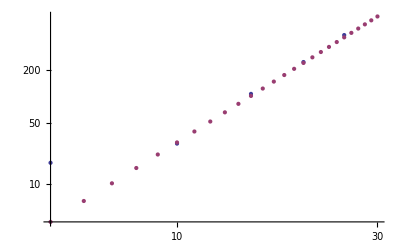

```mathematica
ListLogLogPlot[{bondtime,Table[{x,0.03 x^3},{x,5,30,1}]}]
```

### Mac times

```mathematica
sitetime
```

{{10,3.892148},{20,21.10521},{30,39.361383},{40,60.98989},{50,76.315801},{60,73.439287},{90,100.66224}}

```mathematica
bondtime
```

{{5,5.463399},{10,6.094608},{15,8.155772},{20,12.28982},{25,18.83628},{30,26.20698},{40,50.629215},{50,77.3211}}

```mathematica
rangetime
```

{{1,12.31055},{2,19.7258},{3,28.01656},{4,39.239307},{5,57.504155},{6,67.75259},{7,94.54117}}

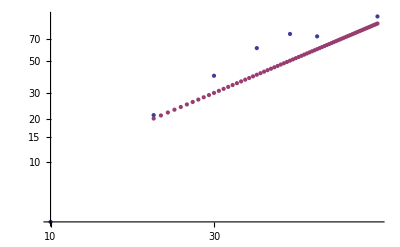

```mathematica
ListLogLogPlot[{sitetime,Table[{x,1 x^1},{x,20,90,1}]}]
```

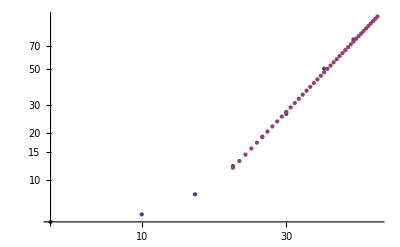

```mathematica
ListLogLogPlot[{bondtime,Table[{x,0.03 x^2},{x,20,60,1}]}]
```

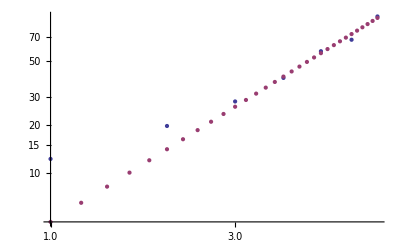

```mathematica
ListLogLogPlot[{rangetime,Table[{x, 5 x^1.5},{x,1,7,0.2}]}]
```

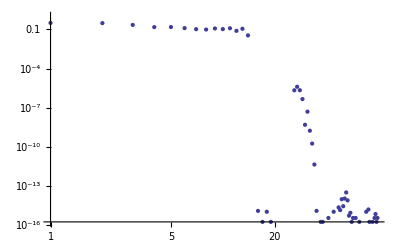

```mathematica
ListLogLogPlot[Table[(energ[[n+1]]-energ[[n]])/energ[[n]],{n,1,Length[energ]-1}]]
```

```mathematica
IsLinkActive[]
```

1

## Time and convergence testing

```mathematica
IsLinkActive[]
```

1

```mathematica
tensors=20;
IntRange=2;
bondtiming=Monitor[MemoryConstrained[Table[{bond,
tiempo=0;
Do[
mps=MPSProductState[tensors,BondDimension->bond];
MPSCanonize[mps];
HMatrix=Table[Table[Piecewise[{{0.0,n==m},{If[α==3,1.0,-0.3]/Abs[n-m]^3,Abs[n-m]≤IntRange}}],{n,1,numTensors},{m,1,numTensors}],{α,1,3}];
tiempo+=AbsoluteTiming[MPSMinimizeEnergy[mps,HMatrix,InteractionRange->IntRange]][[1]];
,{tt,1,10}];
tiempo/10
},{bond,5,12,1}],1024 1024 1024],"Bond dimension: "<>ToString[bond]<>", mem: "<>ToString[MemoryInUse[]/(1024. 1024)]];
```

LinkObject::linkw: Unable to write data to closed link LinkObject["/Users/fercook/Mathematica/MPS/arpackformps", 11452, 8].

Set::shape: Lists {energy$25125, new$25125, info$25125} and $Failed are not the same shape.

LinkObject::linkw: Unable to write data to closed link LinkObject["/Users/fercook/Mathematica/MPS/arpackformps", 11452, 8].

Set::shape: Lists {energy$25125, new$25125, info$25125} and $Failed are not the same shape.

LinkObject::linkw: Unable to write data to closed link LinkObject["/Users/fercook/Mathematica/MPS/arpackformps", 11452, 8].

General::stop: Further output of LinkObject :: "linkw" will be suppressed during this calculation.

Set::shape: Lists {energy$25125, new$25125, info$25125} and $Failed are not the same shape.

General::stop: Further output of Set :: "shape" will be suppressed during this calculation.

Dot::dotsh: Tensors {{-0.685445 - 4.23598×10^-22\ ⅈ, « 6 », -2.69639×10^-8 + 1.40925×10^-6\ ⅈ}, « 6 », {« 23 » + « 22 »\ ⅈ, « 6 », « 21 »  + « 1 »}} and {{-0.00698865 - 0.000541279\ ⅈ, 0.667727  + 0.229217\ ⅈ}, « 2 », {0.0011258  + « 22 »\ ⅈ, « 1 »}} have incompatible shapes.

Dot::dotsh: Tensors {{-0.685445 - 4.23598×10^-22\ ⅈ, « 6 », -2.69639×10^-8 + 1.40925×10^-6\ ⅈ}, « 6 », {« 23 » + « 22 »\ ⅈ, « 6 », « 21 »  + « 1 »}} and {{-0.198647 - 0.679736\ ⅈ, -0.000214457 - 0.00700205\ ⅈ}, « 2 », {0.00199789  - « 21 »\ ⅈ, « 1 »}} have incompatible shapes.

Dot::dotsh: Tensors {{-0.685445 - 4.23598×10^-22\ ⅈ, « 6 », -2.69639×10^-8 + 1.40925×10^-6\ ⅈ}, « 6 », {« 23 » + « 22 »\ ⅈ, « 6 », « 21 »  + « 1 »}} and {{-0.650391 - 0.759535\ ⅈ}, {-0.00812749 - 0.00567109\ ⅈ}} have incompatible shapes.

General::stop: Further output of Dot :: "dotsh" will be suppressed during this calculation.

$Aborted

```mathematica
bond=10;
IntRange=1;
Ntiming=Monitor[MemoryConstrained[Table[{tensors,
mps=MPSProductState[tensors,BondDimension->bond];
MPSCanonize[mps];
HMatrix=Table[Table[Piecewise[{{-0.2,n==m},{If[α==3,1.0,-0.3]/Abs[n-m]^3,Abs[n-m]≤IntRange}}],{n,1,tensors},{m,1,tensors}],{α,1,3}];
AbsoluteTiming[MPSMinimizeEnergy[mps,HMatrix,InteractionRange->IntRange]]
},{tensors,50,100,5}],1024 1024 1024],"Chain Length: "<>ToString[tensors]];
```

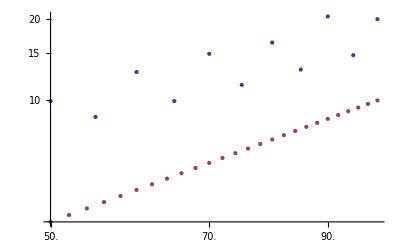

```mathematica
ListLogLogPlot[{{#[[1]],#[[2,1]]}&/@Ntiming,Table[{x,0.01 x^1.5},{x,50,100,2}]}]
```

```mathematica
tensors=20;
bond=10;
Rangetiming=Monitor[MemoryConstrained[Table[{IntRange,
tiempo=0;
Do[
mps=MPSProductState[tensors,BondDimension->bond];
MPSCanonize[mps];
HMatrix=Table[Table[Piecewise[{{-0.5,n==m},{1.0/Abs[n-m]^3,Abs[n-m]≤IntRange}}],{n,1,tensors},{m,1,tensors}],{α,1,3}];
tiempo+=AbsoluteTiming[MPSMinimizeEnergy[mps,HMatrix,InteractionRange->IntRange]][[1]]
,{tt,1,10}];
tiempo/10
},{IntRange,1,8,1}],1024 1024 1024],"Chain Length: "<>ToString[IntRange]];
```

LinkObject::linkw: Unable to write data to closed link LinkObject["/Users/fercook/Mathematica/MPS/arpackformps", 23523, 5].

Set::shape: Lists {energy$18948, new$18948, info$18948} and $Failed are not the same shape.

LinkObject::linkw: Unable to write data to closed link LinkObject["/Users/fercook/Mathematica/MPS/arpackformps", 23523, 5].

Set::shape: Lists {energy$18948, new$18948, info$18948} and $Failed are not the same shape.

LinkObject::linkw: Unable to write data to closed link LinkObject["/Users/fercook/Mathematica/MPS/arpackformps", 23523, 5].

General::stop: Further output of LinkObject :: "linkw" will be suppressed during this calculation.

Set::shape: Lists {energy$18948, new$18948, info$18948} and $Failed are not the same shape.

General::stop: Further output of Set :: "shape" will be suppressed during this calculation.

Dot::dotsh: Tensors {{{-0.726072 + 0.\ ⅈ, 0.581211  + 0.\ ⅈ, « 4 », -0.0932086 + 0.\ ⅈ, 0.0343467  + 0.\ ⅈ}, {« 1 »}, « 1 », {« 1 »}}, « 1 »} and {{0.896067  + 0.\ ⅈ, 0.0232115  + 0.\ ⅈ, « 6 », 1.62606×10^-6 + 0.\ ⅈ, -7.14574×10^-7 + 0.\ ⅈ}, « 8 », {« 1 », « 9 »}} have incompatible shapes.

Dot::dotsh: Tensors {{{0.709299  + 0.\ ⅈ, 0.579102  + 0.\ ⅈ, -0.351197 + 0.\ ⅈ, 0.195441  + 0.\ ⅈ}, {-« 20 » - « 1 », « 2 », « 1 »}}, « 1 »} and {{0.896067  + 0.\ ⅈ, 0.0232115  + 0.\ ⅈ, « 6 », 1.62606×10^-6 + 0.\ ⅈ, -7.14574×10^-7 + 0.\ ⅈ}, « 8 », {« 1 », « 9 »}} have incompatible shapes.

Dot::dotsh: Tensors {{{-0.47479 + 0.\ ⅈ, -0.880099 + 0.\ ⅈ}}, {{-0.821556 + 0.315627\ ⅈ, 0.443207  - « 1 »}}} and {{0.896067  + 0.\ ⅈ, 0.0232115  + 0.\ ⅈ, « 6 », 1.62606×10^-6 + 0.\ ⅈ, -7.14574×10^-7 + 0.\ ⅈ}, « 8 », {« 1 », « 9 »}} have incompatible shapes.

General::stop: Further output of Dot :: "dotsh" will be suppressed during this calculation.

$Aborted

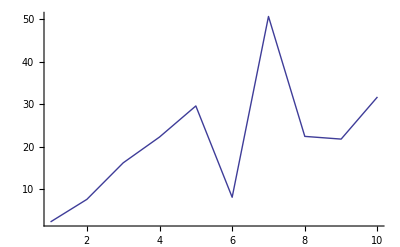

```mathematica
ListPlot[{#[[1]],#[[2,1]]}&/@Rangetiming,Joined->True]
```

## Further testing inside routines

```mathematica
IsLinkActive[]
```

1

```mathematica
mps=MPSProductState[10,BondDimension->10];
MPSCanonize[mps]
numTensors=Length[mps]
chi=.
IntRange=1;HMatrix=Table[Table[Piecewise[{{-0.5,n==m},{1.0,Abs[n-m]≤IntRange}}],{n,1,10},{m,1,10}],{α,1,3}];
```

0

10

```mathematica
defineRight[temp_]:=Module[{fer},
ClearAll[R,fieldR,operatorsR,interactionsR];
R[numTensors+1]={{1}};
R[n_]:=R[n]=RProduct[mps[[n]],mps[[n]],R[n+1]];
fieldR[numTensors+1]=Table[{{0}},{α,1,3}];
fieldR[n_]:=fieldR[n]=Table[
RProduct[mps[[n]],mps[[n]],fieldR[n+1][[α]]]+HMatrix[[α,n,n]]RProduct[sigma[α].mps[[n]],mps[[n]],R[n+1]],{α,1,3}];
operatorsR[numTensors+2]=Table[{},{α,1,3}];
operatorsR[numTensors+1]=Table[{},{α,1,3}];
operatorsR[n_]:=operatorsR[n]=Table[
Prepend[RProduct[mps[[n]],mps[[n]],#]&/@Take[operatorsR[n+1][[α]],Min[IntRange-1,Length[operatorsR[n+1][[α]]]]],RProduct[sigma[α].mps[[n]],mps[[n]],R[n+1]]],{α,1,3}];
interactionsR[numTensors+1]=Table[{{0}},{α,1,3}];
interactionsR[n_]:=interactionsR[n]=Table[
RProduct[mps[[n]],mps[[n]],interactionsR[n+1][[α]]]+(HMatrix[[α,n,n+1;;Min[n+IntRange,numTensors]]].(RProduct[sigma[α].mps[[n]],mps[[n]],#]&/@operatorsR[n+1][[α]])),{α,1,3}];
];
defineLeft[temp_]:=Module[{fer},
ClearAll[L,fieldL,operatorsL,interactionsL];
L[0]={{1}};
L[n_]:=L[n]=LProduct[mps[[n]],mps[[n]],L[n-1]];
fieldL[0]=Table[{{0}},{α,1,3}];
fieldL[n_]:=fieldL[n]=Table[LProduct[mps[[n]],mps[[n]],fieldL[n-1][[α]]]+HMatrix[[α,n,n]]LProduct[sigma[α].mps[[n]],mps[[n]],L[n-1]],{α,1,3}];
operatorsL[-1]=Table[{},{α,1,3}];
operatorsL[0]=Table[{},{α,1,3}];
operatorsL[n_]:=operatorsL[n]=Table[
Prepend[LProduct[mps[[n]],mps[[n]],#]&/@Take[operatorsL[n-1][[α]],-Min[IntRange-1,Length[operatorsL[n-1][[α]]]]],LProduct[sigma[α].mps[[n]],mps[[n]],L[n-1]]],{α,1,3}];
interactionsL[0]=Table[{{0}},{α,1,3}];
interactionsL[n_]:=interactionsL[n]=Table[LProduct[mps[[n]],mps[[n]],interactionsL[n-1][[α]]]+(HMatrix[[α,Max[n-IntRange,1];;n-1,n]].(LProduct[sigma[α].mps[[n]],mps[[n]],#]&/@operatorsL[n-1][[α]])),{α,1,3}];
];
```

```mathematica
defineRight[1]
```

```mathematica
defineLeft[1]
```

```mathematica
can={{1.}};
```

```mathematica
With[{site=1},Dimensions/@{can.#&/@mps[[site]],interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-IntRange];;site,Max[1,site-IntRange];;Min[numTensors,site+IntRange]]]}]
```

{{2,1,10},{3,1,1},{3,10,10},{3,1,1},{3,10,10},{3,0},{3,1,10,10},{3,1,2}}

```mathematica
With[{site=1},TestCommunication[mps[[site]],interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-IntRange];;site,Max[1,site-IntRange];;Min[numTensors,site+IntRange]]]]]
```

{2,1,10,0,1}

```mathematica
With[{site=5},
{energy,new,info}=FindGroundMPSSite[can.#&/@mps[[site]],interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-IntRange];;site,Max[1,site-IntRange];;Min[numTensors,site+IntRange]]]];
mps[[site]]=MPSCanonizeSite[new,can,Direction->"Left",UseMatrix->False]; 
Dimensions[mps[[site]]]
]
```

{2,10,10}

```mathematica
Dimensions[can]
```

{2,10}

```mathematica
Do[
Print["Right sweep:"<>", site:"<>ToString[site]];
{energy,new,info}=FindGroundMPSSite[can.#&/@mps[[site]],interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-IntRange];;site,Max[1,site-IntRange];;Min[numTensors,site+IntRange]]],InteractionRange->IntRange];
mps[[site]]=MPSCanonizeSite[new,can,Direction->"Left",UseMatrix->False]; (* This routine changes canon *)
,{site,1,numTensors}];
```

Right sweep:, site:1

Right sweep:, site:2

Right sweep:, site:3

Right sweep:, site:4

Right sweep:, site:5

Right sweep:, site:6

Right sweep:, site:7

Right sweep:, site:8

Right sweep:, site:9

Right sweep:, site:10

```mathematica
energy
```

-17.1795

```mathematica
Dimensions/@mps
```

{{2,1,2},{2,2,4},{2,4,8},{2,8,10},{2,10,10},{2,10,10},{2,10,8},{2,8,4},{2,4,2},{2,2,1}}

```mathematica
Dimensions[can]
```

{1,1}

```mathematica
defineRight[1]
```

```mathematica
Manipulate[Chop[L[n]]//MatrixForm,{n,0,9,1}]
```

```mathematica
Do[
Print["Left sweep:"<>", site:"<>ToString[site]];
Print[Dimensions/@{mps[[site]].can,interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-1];;site,Max[1,site-1];;Min[numTensors,site+1]]]}];
{energy,new,info}=FindGroundMPSSite[mps[[site]].can,interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-1];;site,Max[1,site-1];;Min[numTensors,site+1]]]];
mps[[site]]=MPSCanonizeSite[new,can,UseMatrix->False];
,{site,numTensors,1,-1}];
```

Left sweep:, site:10

{{2,2,1},{3,2,2},{3,1,1},{3,2,2},{3,1,1},{3,1,2,2},{3,0},{3,2,2}}

Left sweep:, site:9

{{2,4,2},{3,4,4},{3,2,2},{3,4,4},{3,2,2},{3,1,4,4},{3,1,2,2},{3,2,3}}

Left sweep:, site:8

{{2,8,4},{3,8,8},{3,4,4},{3,8,8},{3,4,4},{3,1,8,8},{3,1,4,4},{3,2,3}}

Left sweep:, site:7

{{2,10,8},{3,10,10},{3,8,8},{3,10,10},{3,8,8},{3,1,10,10},{3,1,8,8},{3,2,3}}

Left sweep:, site:6

{{2,10,10},{3,10,10},{3,10,10},{3,10,10},{3,10,10},{3,1,10,10},{3,1,10,10},{3,2,3}}

Left sweep:, site:5

{{2,10,10},{3,10,10},{3,10,10},{3,10,10},{3,10,10},{3,1,10,10},{3,1,10,10},{3,2,3}}

Left sweep:, site:4

{{2,8,10},{3,8,8},{3,10,10},{3,8,8},{3,10,10},{3,1,8,8},{3,1,10,10},{3,2,3}}

Left sweep:, site:3

{{2,4,8},{3,4,4},{3,8,8},{3,4,4},{3,8,8},{3,1,4,4},{3,1,8,8},{3,2,3}}

Left sweep:, site:2

{{2,2,4},{3,2,2},{3,4,4},{3,2,2},{3,4,4},{3,1,2,2},{3,1,4,4},{3,2,3}}

Left sweep:, site:1

{{2,1,2},{3,1,1},{3,2,2},{3,1,1},{3,2,2},{3,0},{3,1,2,2},{3,1,2}}

```mathematica
Dimensions/@mps
```

{{2,1,2},{2,2,4},{2,4,8},{2,8,10},{2,10,10},{2,10,10},{2,10,8},{2,8,4},{2,4,2},{2,2,1}}

```mathematica
Dimensions[can]
```

{1,1}

```mathematica
can
```

{{1.+0. ⅈ}}

```mathematica
Manipulate[Chop[R[n]]//MatrixForm,{n,2,11,1}]
```

```mathematica
defineLeft[1]
```

```mathematica
can.#&/@mps[[1]]
```

{{{-0.168019+0.751672 ⅈ,-0.155312-0.149617 ⅈ}},{{-0.345661+0.206303 ⅈ,0.00472112+0.445182 ⅈ}}}

```mathematica
Dimensions[mps[[1]]]
```

{2,1,2}

```mathematica
Do[
Print["Right sweep:"<>", site:"<>ToString[site]];
Print[Dimensions/@{can.#&/@mps[[site]],interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-1];;site,Max[1,site-1];;Min[numTensors,site+1]]]}];
{energy,new,info}=FindGroundMPSSite[can.#&/@mps[[site]],interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-1];;site,Max[1,site-1];;Min[numTensors,site+1]]]];
mps[[site]]=MPSCanonizeSite[new,can,Direction->"Left",UseMatrix->False]; (* This routine changes canon *)
,{site,1,5}];
```

Right sweep:, site:1

{{2,1,2},{3,1,1},{3,2,2},{3,1,1},{3,2,2},{3,0},{3,1,2,2},{3,1,2}}

Right sweep:, site:2

{{2,2,4},{3,2,2},{3,4,4},{3,2,2},{3,4,4},{3,1,2,2},{3,1,4,4},{3,2,3}}

Right sweep:, site:3

{{2,4,8},{3,4,4},{3,8,8},{3,4,4},{3,8,8},{3,1,4,4},{3,1,8,8},{3,2,3}}

Right sweep:, site:4

{{2,8,10},{3,8,8},{3,10,10},{3,8,8},{3,10,10},{3,1,8,8},{3,1,10,10},{3,2,3}}

Right sweep:, site:5

{{2,10,10},{3,10,10},{3,10,10},{3,10,10},{3,10,10},{3,1,10,10},{3,1,10,10},{3,2,3}}

```mathematica
MPSCanonizationCheck[mps,Site->6]
```

True

```mathematica
mps=MPSProductState[10,BondDimension->10];
MPSCanonize[mps,Site->11]
MPSCanonize[mps]
```

Part::pspec: Part specification i$ is neither an integer nor a list of integers.

General::stop: Further output of Part :: "pspec" will be suppressed during this calculation.

11

0

```mathematica
Dimensions/@mps
```

{{2,1,2},{2,2,4},{2,4,8},{2,8,10},{2,10,10},{2,10,10},{2,10,8},{2,8,4},{2,4,2},{2,2,1}}

## Multiplication of vectors

```mathematica
mps=MPSProductState[10,BondDimension->10];
MPSCanonize[mps]
numTensors=Length[mps]
can={{1.}}
IntRange=3;HMatrix=Table[Table[Piecewise[{{-0.5,n==m},{1.0,Abs[n-m]≤IntRange}}],{n,1,10},{m,1,10}],{α,1,3}];
```

0

10

{{1.}}

```mathematica
defineRight[temp_]:=Module[{fer},
ClearAll[R,fieldR,operatorsR,interactionsR];
R[numTensors+1]={{1}};
R[n_]:=R[n]=RProduct[mps[[n]],mps[[n]],R[n+1]];
fieldR[numTensors+1]=Table[{{0}},{α,1,3}];
fieldR[n_]:=fieldR[n]=Table[
RProduct[mps[[n]],mps[[n]],fieldR[n+1][[α]]]+HMatrix[[α,n,n]]RProduct[sigma[α].mps[[n]],mps[[n]],R[n+1]],{α,1,3}];
operatorsR[numTensors+2]=Table[{},{α,1,3}];
operatorsR[numTensors+1]=Table[{},{α,1,3}];
operatorsR[n_]:=operatorsR[n]=Table[
Prepend[RProduct[mps[[n]],mps[[n]],#]&/@Take[operatorsR[n+1][[α]],Min[IntRange-1,Length[operatorsR[n+1][[α]]]]],RProduct[sigma[α].mps[[n]],mps[[n]],R[n+1]]],{α,1,3}];
interactionsR[numTensors+1]=Table[{{0}},{α,1,3}];
interactionsR[n_]:=interactionsR[n]=Table[
RProduct[mps[[n]],mps[[n]],interactionsR[n+1][[α]]]+(HMatrix[[α,n,n+1;;Min[n+IntRange,numTensors]]].(RProduct[sigma[α].mps[[n]],mps[[n]],#]&/@operatorsR[n+1][[α]])),{α,1,3}];
];
defineLeft[temp_]:=Module[{fer},
ClearAll[L,fieldL,operatorsL,interactionsL];
L[0]={{1}};
L[n_]:=L[n]=LProduct[mps[[n]],mps[[n]],L[n-1]];
fieldL[0]=Table[{{0}},{α,1,3}];
fieldL[n_]:=fieldL[n]=Table[LProduct[mps[[n]],mps[[n]],fieldL[n-1][[α]]]+HMatrix[[α,n,n]]LProduct[sigma[α].mps[[n]],mps[[n]],L[n-1]],{α,1,3}];
operatorsL[-1]=Table[{},{α,1,3}];
operatorsL[0]=Table[{},{α,1,3}];
operatorsL[n_]:=operatorsL[n]=Table[
Prepend[LProduct[mps[[n]],mps[[n]],#]&/@Take[operatorsL[n-1][[α]],-Min[IntRange-1,Length[operatorsL[n-1][[α]]]]],LProduct[sigma[α].mps[[n]],mps[[n]],L[n-1]]],{α,1,3}];
interactionsL[0]=Table[{{0}},{α,1,3}];
interactionsL[n_]:=interactionsL[n]=Table[LProduct[mps[[n]],mps[[n]],interactionsL[n-1][[α]]]+(HMatrix[[α,Max[n-IntRange,1];;n-1,n]].(LProduct[sigma[α].mps[[n]],mps[[n]],#]&/@operatorsL[n-1][[α]])),{α,1,3}];
];
```

```mathematica
defineLeft[1]
```

```mathematica
defineRight[2]
```

```mathematica
testsite=1;
```

```mathematica
IsLinkActive[]
```

1

```mathematica
With[{site=testsite},Dimensions/@{can.#&/@mps[[site]],interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-IntRange];;site,Max[1,site-IntRange];;Min[numTensors,site+IntRange]]]}]
```

{{2,1,10},{3,1,1},{3,10,10},{3,1,1},{3,10,10},{3,0},{3,3,10,10},{3,1,4}}

```mathematica
With[{site=testsite},temp=can.#&/@mps[[site]];Timing[new=MPSMatrixVector[can.#&/@mps[[site]],temp,interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-IntRange];;site,Max[1,site-IntRange];;Min[numTensors,site+IntRange]]]]];
];
With[{site=testsite},temp=can.#&/@mps[[site]];Timing[Heff=MPSEffectiveHam[interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-IntRange];;site,Max[1,site-IntRange];;Min[numTensors,site+IntRange]]]]];
Dimensions[old=Partition[Partition[Heff.Flatten[temp],10],1]]];
new
old
```

{{{-0.0560186-0.21326 ⅈ,0.461421-0.175491 ⅈ,0.612438-0.591175 ⅈ,-0.228629-0.393008 ⅈ,0.435909+0.598353 ⅈ,-0.389152-0.320987 ⅈ,-0.0997853-0.188409 ⅈ,-0.693887-0.0566196 ⅈ,-0.514679+0.832473 ⅈ,0.774377+0.297311 ⅈ}},{{0.542634+1.82022 ⅈ,0.667307+0.213043 ⅈ,-0.407106-0.267685 ⅈ,0.315313-0.268035 ⅈ,-0.104845-0.386461 ⅈ,1.64599+0.351817 ⅈ,-0.363001+0.467425 ⅈ,-0.044365+0.131434 ⅈ,0.758998+0.639946 ⅈ,0.115352-0.0131276 ⅈ}}}

{{{-0.0560186-0.21326 ⅈ,0.461421-0.175491 ⅈ,0.612438-0.591175 ⅈ,-0.228629-0.393008 ⅈ,0.435909+0.598353 ⅈ,-0.389152-0.320987 ⅈ,-0.0997853-0.188409 ⅈ,-0.693887-0.0566196 ⅈ,-0.514679+0.832473 ⅈ,0.774377+0.297311 ⅈ}},{{0.542634+1.82022 ⅈ,0.667307+0.213043 ⅈ,-0.407106-0.267685 ⅈ,0.315313-0.268035 ⅈ,-0.104845-0.386461 ⅈ,1.64599+0.351817 ⅈ,-0.363001+0.467425 ⅈ,-0.044365+0.131434 ⅈ,0.758998+0.639946 ⅈ,0.115352-0.0131276 ⅈ}}}

```mathematica
With[{site=1},
{energy,new,info}=FindGroundMPSSite[can.#&/@mps[[site]],interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-IntRange];;site,Max[1,site-IntRange];;Min[numTensors,site+IntRange]]]];
mps[[site]]=MPSCanonizeSite[new,can,Direction->"Left",UseMatrix->False]; 
Dimensions[mps[[site]]]
]
```

{2,1,2}

```mathematica
testsite=2
```

2

```mathematica
With[{site=testsite},Dimensions/@{can.#&/@mps[[site]],interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-IntRange];;site,Max[1,site-IntRange];;Min[numTensors,site+IntRange]]]}]
```

{{2,2,10},{3,2,2},{3,10,10},{3,2,2},{3,10,10},{3,1,2,2},{3,3,10,10},{3,2,5}}

```mathematica
With[{site=testsite},temp=can.#&/@mps[[site]];Timing[new=MPSMatrixVector[can.#&/@mps[[site]],temp,interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-IntRange];;site,Max[1,site-IntRange];;Min[numTensors,site+IntRange]]]]];
];
With[{site=testsite},temp=can.#&/@mps[[site]];Timing[Heff=MPSEffectiveHam[interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-IntRange];;site,Max[1,site-IntRange];;Min[numTensors,site+IntRange]]]]];
Dimensions[old=Partition[Partition[Heff.Flatten[temp],10],1]]];
new
old
```

{{{0.219043-0.251266 ⅈ,0.803518+0.50262 ⅈ,1.071-0.509902 ⅈ,-1.40666+0.419866 ⅈ,-0.658436-0.823457 ⅈ,-0.640241+0.580391 ⅈ,0.200989+0.577497 ⅈ,-1.34737+1.31941 ⅈ,-0.574657-0.142811 ⅈ,0.43198-0.164369 ⅈ},{-0.330809+0.00624833 ⅈ,0.252091-1.1127 ⅈ,-0.743509-1.02649 ⅈ,0.384562+0.682718 ⅈ,1.13807+0.445329 ⅈ,1.66783+1.00651 ⅈ,-0.117258-1.04065 ⅈ,-0.423414-0.468936 ⅈ,0.324413+0.653281 ⅈ,0.406948-0.0508901 ⅈ}},{{0.145327+0.494211 ⅈ,-0.611925+0.197458 ⅈ,-0.599226+0.304567 ⅈ,-0.797715-0.0149795 ⅈ,1.3925-1.5673 ⅈ,1.54113-1.18195 ⅈ,-0.898298-0.886156 ⅈ,-1.37371-0.192527 ⅈ,-0.032336-0.256243 ⅈ,0.833378+0.303713 ⅈ},{-0.0228355-0.077223 ⅈ,0.190691-0.168775 ⅈ,0.067844-0.338904 ⅈ,0.0209345+0.224164 ⅈ,0.78668-0.0507071 ⅈ,0.545231+0.0152117 ⅈ,-0.656642-0.961745 ⅈ,-0.572815-0.314571 ⅈ,0.396123-0.0445791 ⅈ,0.331645-0.428356 ⅈ}}}

{{{0.219043-0.251266 ⅈ,0.803518+0.50262 ⅈ,1.071-0.509902 ⅈ,-1.40666+0.419866 ⅈ,-0.658436-0.823457 ⅈ,-0.640241+0.580391 ⅈ,0.200989+0.577497 ⅈ,-1.34737+1.31941 ⅈ,-0.574657-0.142811 ⅈ,0.43198-0.164369 ⅈ}},{{-0.330809+0.00624833 ⅈ,0.252091-1.1127 ⅈ,-0.743509-1.02649 ⅈ,0.384562+0.682718 ⅈ,1.13807+0.445329 ⅈ,1.66783+1.00651 ⅈ,-0.117258-1.04065 ⅈ,-0.423414-0.468936 ⅈ,0.324413+0.653281 ⅈ,0.406948-0.0508901 ⅈ}},{{0.145327+0.494211 ⅈ,-0.611925+0.197458 ⅈ,-0.599226+0.304567 ⅈ,-0.797715-0.0149795 ⅈ,1.3925-1.5673 ⅈ,1.54113-1.18195 ⅈ,-0.898298-0.886156 ⅈ,-1.37371-0.192527 ⅈ,-0.032336-0.256243 ⅈ,0.833378+0.303713 ⅈ}},{{-0.0228355-0.077223 ⅈ,0.190691-0.168775 ⅈ,0.067844-0.338904 ⅈ,0.0209345+0.224164 ⅈ,0.78668-0.0507071 ⅈ,0.545231+0.0152117 ⅈ,-0.656642-0.961745 ⅈ,-0.572815-0.314571 ⅈ,0.396123-0.0445791 ⅈ,0.331645-0.428356 ⅈ}}}

## Other things

```mathematica
defineRight[1]
```

```mathematica
Do[
Print["Left sweep:"<>", site:"<>ToString[site]];
Print[Dimensions/@{mps[[site]].can,interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-1];;site,Max[1,site-1];;Min[numTensors,site+1]]]}];
{energy,new,info}=FindGroundMPSSite[mps[[site]].can,interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-1];;site,Max[1,site-1];;Min[numTensors,site+1]]]];
mps[[site]]=MPSCanonizeSite[new,can,UseMatrix->False];
,{site,numTensors,1,-1}];
```

Left sweep:, site:10

{{2,2,1},{3,2,2},{3,1,1},{3,2,2},{3,1,1},{3,1,2,2},{3,0},{3,2,2}}

Left sweep:, site:9

{{2,4,2},{3,4,4},{3,2,2},{3,4,4},{3,2,2},{3,1,4,4},{3,1,2,2},{3,2,3}}

Left sweep:, site:8

{{2,8,4},{3,8,8},{3,4,4},{3,8,8},{3,4,4},{3,1,8,8},{3,1,4,4},{3,2,3}}

Left sweep:, site:7

{{2,10,8},{3,10,10},{3,8,8},{3,10,10},{3,8,8},{3,1,10,10},{3,1,8,8},{3,2,3}}

Left sweep:, site:6

{{2,10,10},{3,10,10},{3,10,10},{3,10,10},{3,10,10},{3,1,10,10},{3,1,10,10},{3,2,3}}

Left sweep:, site:5

{{2,10,10},{3,10,10},{3,10,10},{3,10,10},{3,10,10},{3,1,10,10},{3,1,10,10},{3,2,3}}

Left sweep:, site:4

{{2,8,10},{3,8,8},{3,10,10},{3,8,8},{3,10,10},{3,1,8,8},{3,1,10,10},{3,2,3}}

Left sweep:, site:3

{{2,4,8},{3,4,4},{3,8,8},{3,4,4},{3,8,8},{3,1,4,4},{3,1,8,8},{3,2,3}}

Left sweep:, site:2

{{2,2,4},{3,2,2},{3,4,4},{3,2,2},{3,4,4},{3,1,2,2},{3,1,4,4},{3,2,3}}

Left sweep:, site:1

{{2,1,2},{3,1,1},{3,2,2},{3,1,1},{3,2,2},{3,0},{3,1,2,2},{3,1,2}}

```mathematica
With[{site=1},TestCommunication[can.#&/@mps[[site]],interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-1];;site,Max[1,site-1];;Min[numTensors,site+1]]]]
]
```

{2,1,10,0,1}

```mathematica
With[{site=1},{energy,new,info}=FindGroundMPSSite[can.#&/@mps[[site]],interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-1];;site,Max[1,site-1];;Min[numTensors,site+1]]]];
mps[[site]]=MPSCanonizeSite[new,can,Direction->"Left",UseMatrix->False]]
```

{{{0.825876+0. ⅈ,0.563851+0. ⅈ}},{{0.36056+0.433503 ⅈ,-0.528114-0.634954 ⅈ}}}

```mathematica
energy
Dimensions[mps[[1]]]
Dimensions[can]
Dimensions[mps[[2]]]
```

-5.1062

{2,1,2}

{2,10}

{2,10,10}

```mathematica
With[{site=2},{energy,new,info}=FindGroundMPSSite[can.#&/@mps[[site]],interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-1];;site,Max[1,site-1];;Min[numTensors,site+1]]]];
mps[[site]]=MPSCanonizeSite[new,can,Direction->"Left",UseMatrix->False]]
```

{{{-0.43568+0. ⅈ,-0.877253+0. ⅈ,0.150366+0. ⅈ,0.134168+0. ⅈ},{0.44467-0.0431388 ⅈ,-0.161768-0.0496261 ⅈ,0.607127-0.543745 ⅈ,-0.294174+0.144827 ⅈ}},{{0.556017+0.396425 ⅈ,-0.400072-0.191564 ⅈ,-0.536331+0.0642082 ⅈ,-0.209239-0.0371958 ⅈ},{0.239094+0.295156 ⅈ,0.0238976-0.0668623 ⅈ,0.141236+0.0375055 ⅈ,0.77437+0.479242 ⅈ}}}

```mathematica
energy
Dimensions[mps[[2]]]
Dimensions[can]
Dimensions[mps[[3]]]
```

-7.05812

{2,2,4}

{4,10}

{2,10,10}

```mathematica
With[{site=3},{energy,new,info}=FindGroundMPSSite[can.#&/@mps[[site]],interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-1];;site,Max[1,site-1];;Min[numTensors,site+1]]]];
mps[[site]]=MPSCanonizeSite[new,can,Direction->"Left",UseMatrix->False];]
```

```mathematica
energy
Dimensions[mps[[3]]]
Dimensions[can]
Dimensions[mps[[4]]]
```

-9.11617

{2,4,8}

{8,10}

{2,10,10}

```mathematica
With[{site=4},{energy,new,info}=FindGroundMPSSite[can.#&/@mps[[site]],interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-1];;site,Max[1,site-1];;Min[numTensors,site+1]]]];
Dimensions[mps[[site]]=MPSCanonizeSite[new,can,Direction->"Left",UseMatrix->False]]]
```

{2,8,10}

```mathematica
energy
Dimensions[mps[[4]]]
Dimensions[can]
Dimensions[mps[[5]]]
```

-10.0956

{2,8,10}

{10,10}

{2,10,10}

```mathematica
With[{site=5},{energy,new,info}=FindGroundMPSSite[can.#&/@mps[[site]],interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-1];;site,Max[1,site-1];;Min[numTensors,site+1]]]];
Dimensions[mps[[site]]=MPSCanonizeSite[new,can,Direction->"Left",UseMatrix->False]]]
```

{2,10,10}

```mathematica
energy
Dimensions[mps[[5]]]
Dimensions[can]
Dimensions[mps[[6]]]
```

-12.8379

{2,10,10}

{10,10}

{2,10,10}

```mathematica
With[{site=6},{energy,new,info}=FindGroundMPSSite[can.#&/@mps[[site]],interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-1];;site,Max[1,site-1];;Min[numTensors,site+1]]]];
Dimensions[mps[[site]]=MPSCanonizeSite[new,can,Direction->"Left",UseMatrix->False]]]
```

{2,10,10}

```mathematica
energy
Dimensions[mps[[6]]]
Dimensions[can]
Dimensions[mps[[7]]]
```

-15.3523

{2,10,10}

{10,10}

{2,10,8}

```mathematica
MPSCanonizationCheck[mps,Site->7]
```

True

```mathematica
With[{site=7},{energy,new,info}=FindGroundMPSSite[can.#&/@mps[[site]],interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-1];;site,Max[1,site-1];;Min[numTensors,site+1]]]];
Dimensions[mps[[site]]=MPSCanonizeSite[new,can,Direction->"Left",UseMatrix->False]]]
```

{2,10,8}

```mathematica
energy
Dimensions[mps[[7]]]
Dimensions[can]
Dimensions[mps[[8]]]
```

-17.3179

{2,10,8}

{8,8}

{2,8,4}

```mathematica
MPSCanonizationCheck[mps,Site->8]
```

True

```mathematica
With[{site=8},{energy,new,info}=FindGroundMPSSite[can.#&/@mps[[site]],interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-1];;site,Max[1,site-1];;Min[numTensors,site+1]]]];
Dimensions[mps[[site]]=MPSCanonizeSite[new,can,Direction->"Left",UseMatrix->False]]]
```

{2,8,4}

```mathematica
energy
Dimensions[mps[[8]]]
Dimensions[can]
Dimensions[mps[[9]]]
```

-17.3448

{2,8,4}

{4,4}

{2,4,2}

```mathematica
With[{site=9},{energy,new,info}=FindGroundMPSSite[can.#&/@mps[[site]],interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-1];;site,Max[1,site-1];;Min[numTensors,site+1]]]];
Dimensions[mps[[site]]=MPSCanonizeSite[new,can,Direction->"Left",UseMatrix->False]]]
```

{2,4,2}

```mathematica
energy
Dimensions[mps[[9]]]
Dimensions[can]
Dimensions[mps[[10]]]
```

-17.3473

{2,4,2}

{2,2}

{2,2,1}

```mathematica
With[{site=10},{energy,new,info}=FindGroundMPSSiteManual[can.#&/@mps[[site]],interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-1];;site,Max[1,site-1];;Min[numTensors,site+1]]]]
]
```

{{-17.3794-4.60466×10^-16 ⅈ},{{{0.724954-0.276337 ⅈ},{-0.176591+0.162172 ⅈ}},{{0.370933+0.174527 ⅈ},{0.411569+0.0561781 ⅈ}}}}

```mathematica
With[{site=10},MPSEffectiveHam[interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-1];;site,Max[1,site-1];;Min[numTensors,site+1]]]]
].{1,1,1,1}//Normal
```

{-17.1008+1.79736 ⅈ,-13.1343-0.736058 ⅈ,-15.4747-0.745439 ⅈ,-15.9091-0.31586 ⅈ}

```mathematica
With[{site=10},{energy,new,info}=FindGroundMPSSite[can.#&/@mps[[site]],interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-1];;site,Max[1,site-1];;Min[numTensors,site+1]]]]
]
```

{-17.1798,{{{0.019601+0.706628 ⅈ},{-0.0133275-0.284471 ⅈ}},{{-0.265972+0.259077 ⅈ},{-0.397937+0.350679 ⅈ}}}}

```mathematica
defineRight[1]
```

```mathematica
With[{site=10},Dimensions[mps[[site]]=MPSCanonizeSite[new,can,UseMatrix->False]]]
```

{2,2,1}

```mathematica
With[{site=9},{energy,new,info}=FindGroundMPSSite[mps[[site]].can,interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-1];;site,Max[1,site-1];;Min[numTensors,site+1]]]];
Dimensions[mps[[site]]=MPSCanonizeSite[new,can,UseMatrix->False]]]
energy
Dimensions[mps[[9]]]
Dimensions[can]
Dimensions[mps[[10]]]
```

{2,4,2}

-17.3473

{2,4,2}

{4,4}

{2,2,1}

```mathematica
With[{site=8},{energy,new,info}=FindGroundMPSSite[mps[[site]].can,interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-1];;site,Max[1,site-1];;Min[numTensors,site+1]]]];
Dimensions[mps[[site]]=MPSCanonizeSite[new,can,UseMatrix->False]]]
energy
Dimensions[mps[[9]]]
Dimensions[can]
Dimensions[mps[[10]]]
```

{2,8,4}

-17.3448

{2,4,2}

{8,8}

{2,2,1}

```mathematica
With[{site=7},{energy,new,info}=FindGroundMPSSite[mps[[site]].can,interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-1];;site,Max[1,site-1];;Min[numTensors,site+1]]]];
Dimensions[mps[[site]]=MPSCanonizeSite[new,can,UseMatrix->False]]]
energy
Dimensions[mps[[9]]]
Dimensions[can]
Dimensions[mps[[10]]]
```

{2,10,8}

-17.3179

{2,4,2}

{10,10}

{2,2,1}

```mathematica
With[{site=6},{energy,new,info}=FindGroundMPSSite[mps[[site]].can,interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-1];;site,Max[1,site-1];;Min[numTensors,site+1]]]];
Dimensions[mps[[site]]=MPSCanonizeSite[new,can,UseMatrix->False]]]
energy
Dimensions[mps[[5]]]
Dimensions[can]
Dimensions[mps[[6]]]
```

{2,10,10}

-17.3895

{2,10,10}

{10,10}

{2,10,10}

```mathematica
With[{site=5},{energy,new,info}=FindGroundMPSSite[mps[[site]].can,interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-1];;site,Max[1,site-1];;Min[numTensors,site+1]]]];
Dimensions[mps[[site]]=MPSCanonizeSite[new,can,UseMatrix->False]]]
energy
Dimensions[mps[[4]]]
Dimensions[can]
Dimensions[mps[[5]]]
```

{2,10,10}

-17.341

{2,8,10}

{10,10}

{2,10,10}

```mathematica
With[{site=4},{energy,new,info}=FindGroundMPSSite[mps[[site]].can,interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-1];;site,Max[1,site-1];;Min[numTensors,site+1]]]];
Dimensions[mps[[site]]=MPSCanonizeSite[new,can,UseMatrix->False]]]
energy
Dimensions[mps[[9]]]
Dimensions[can]
Dimensions[mps[[10]]]
```

{2,8,10}

-17.384

{2,4,2}

{8,8}

{2,2,1}

```mathematica
With[{site=3},{energy,new,info}=FindGroundMPSSite[mps[[site]].can,interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-1];;site,Max[1,site-1];;Min[numTensors,site+1]]]];
Dimensions[mps[[site]]=MPSCanonizeSite[new,can,UseMatrix->False]]]
energy
Dimensions[mps[[2]]]
Dimensions[can]
Dimensions[mps[[3]]]
```

{2,4,8}

-17.3011

{2,2,4}

{4,4}

{2,4,8}

```mathematica
With[{site=2},{energy,new,info}=FindGroundMPSSite[mps[[site]].can,interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-1];;site,Max[1,site-1];;Min[numTensors,site+1]]]];
Dimensions[mps[[site]]=MPSCanonizeSite[new,can,UseMatrix->False]]]
energy
Dimensions[mps[[1]]]
Dimensions[can]
Dimensions[mps[[2]]]
```

{2,2,4}

-17.2831

{2,1,2}

{2,2}

{2,2,4}

```mathematica
Length[fieldL[0][[1]]]
```

1

```mathematica
With[{site=1},Dimensions/@{mps[[site]].can,interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-1];;site,Max[1,site-1];;Min[numTensors,site+1]]]}
]
```

{{2,1,2},{3,1,1},{3,2,2},{3,1,1},{3,2,2},{3,0},{3,1,2,2},{3,1,2}}

```mathematica
With[{site=1},TestCommunication[mps[[site]].can,interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-1];;site,Max[1,site-1];;Min[numTensors,site+1]]]]
]
```

{2,1,2,0,1}

```mathematica
With[{site=1},{energy,new,info}=FindGroundMPSSite[mps[[site]].can,interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-1];;site,Max[1,site-1];;Min[numTensors,site+1]]]];
Dimensions[mps[[site]]=MPSCanonizeSite[new,can,UseMatrix->False]]]
energy
Dimensions[mps[[1]]]
Dimensions[can]
Dimensions[mps[[2]]]
```

{2,1,2}

-17.2812

{2,1,2}

{1,1}

{2,2,4}

```mathematica
can
```

{{1.+0. ⅈ}}

```mathematica
Chop[can]
```

{{1.}}

```mathematica
defineLeft[1]
```

```mathematica
With[{site=1},TestCommunication[can.#&/@mps[[site]],interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-1];;site,Max[1,site-1];;Min[numTensors,site+1]]]]
]
```

{2,1,2,0,1}

```mathematica
With[{site=1},{energy,new,info}=FindGroundMPSSite[can.#&/@mps[[site]],interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-1];;site,Max[1,site-1];;Min[numTensors,site+1]]]];
{Dimensions[mps[[site]]=MPSCanonizeSite[new,can,Direction->"Left",UseMatrix->False],]
energy,
Dimensions[mps[[site]]],
Dimensions[can],
Dimensions[mps[[site+1]]]}]
```

{-138.249,-34.5623,-276.499}

```mathematica
energy
Dimensions[mps[[1]]]
Dimensions[can]
Dimensions[mps[[1+1]]]
```

-17.2812

{2,1,2}

{2,2}

{2,2,4}

```mathematica
With[{site=2},{energy,new,info}=FindGroundMPSSite[can.#&/@mps[[site]],interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-1];;site,Max[1,site-1];;Min[numTensors,site+1]]]];
{Dimensions[mps[[site]]=MPSCanonizeSite[new,can,Direction->"Left",UseMatrix->False]],
energy,
Dimensions[mps[[site]]],
Dimensions[can],
Dimensions[mps[[site+1]]]}]
```

Dimensions::innf: Non-negative integer or Infinity expected at position 2 in Dimensions[{{{0.412285  + 0.\ ⅈ, -0.891161 + 0.\ ⅈ, 0.188195  + 0.\ ⅈ, -0.0208746 + 0.\ ⅈ}, {0.430618  + 0.0931721\ ⅈ, « 1 », « 1 », -0.430575 + 0.245416\ ⅈ}}, « 1 »}, « 4 »].

{-17.2831 Dimensions[{{{0.412285+0. ⅈ,-0.891161+0. ⅈ,0.188195+0. ⅈ,-0.0208746+0. ⅈ},{0.430618+0.0931721 ⅈ,0.0592995-0.0108311 ⅈ,-0.710325-0.228182 ⅈ,-0.430575+0.245416 ⅈ}},{{-0.505568-0.563071 ⅈ,-0.294904-0.338638 ⅈ,-0.289581-0.374451 ⅈ,-0.00618344-0.0399859 ⅈ},{0.116242+0.223042 ⅈ,-0.0120346+0.0202363 ⅈ,-0.218421-0.369019 ⅈ,0.84044+0.214391 ⅈ}}},Null],{2,2,4},{4,4},{2,4,8}}

```mathematica
With[{site=3},{energy,new,info}=FindGroundMPSSite[can.#&/@mps[[site]],interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-1];;site,Max[1,site-1];;Min[numTensors,site+1]]]];
{Dimensions[mps[[site]]=MPSCanonizeSite[new,can,Direction->"Left",UseMatrix->False]],
energy,
Dimensions[mps[[site]]],
Dimensions[can],
Dimensions[mps[[site+1]]]}]
```

{{2,4,8},-17.3011,{2,4,8},{8,8},{2,8,10}}

```mathematica
With[{site=4},{energy,new,info}=FindGroundMPSSite[can.#&/@mps[[site]],interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-1];;site,Max[1,site-1];;Min[numTensors,site+1]]]];
{Dimensions[mps[[site]]=MPSCanonizeSite[new,can,Direction->"Left",UseMatrix->False]],
energy,
Dimensions[mps[[site]]],
Dimensions[can],
Dimensions[mps[[site+1]]]}]
```

{{2,8,10},-17.384,{2,8,10},{10,10},{2,10,10}}

```mathematica
With[{site=5},{energy,new,info}=FindGroundMPSSite[can.#&/@mps[[site]],interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-1];;site,Max[1,site-1];;Min[numTensors,site+1]]]];
{Dimensions[mps[[site]]=MPSCanonizeSite[new,can,Direction->"Left",UseMatrix->False]],
energy,
Dimensions[mps[[site]]],
Dimensions[can],
Dimensions[mps[[site+1]]]}]
```

{{2,10,10},-17.342,{2,10,10},{10,10},{2,10,10}}

```mathematica
With[{site=6},{energy,new,info}=FindGroundMPSSite[can.#&/@mps[[site]],interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-1];;site,Max[1,site-1];;Min[numTensors,site+1]]]];
{Dimensions[mps[[site]]=MPSCanonizeSite[new,can,Direction->"Left",UseMatrix->False]],
energy,
Dimensions[mps[[site]]],
Dimensions[can],
Dimensions[mps[[site+1]]]}]
```

{{2,10,10},-17.3906,{2,10,10},{10,10},{2,10,8}}

```mathematica
With[{site=7},{energy,new,info}=FindGroundMPSSite[can.#&/@mps[[site]],interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-1];;site,Max[1,site-1];;Min[numTensors,site+1]]]];
{Dimensions[mps[[site]]=MPSCanonizeSite[new,can,Direction->"Left",UseMatrix->False]],
energy,
Dimensions[mps[[site]]],
Dimensions[can],
Dimensions[mps[[site+1]]]}]
```

{{2,10,8},-17.3226,{2,10,8},{8,8},{2,8,4}}

```mathematica
With[{site=8},{energy,new,info}=FindGroundMPSSite[can.#&/@mps[[site]],interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-1];;site,Max[1,site-1];;Min[numTensors,site+1]]]];
{Dimensions[mps[[site]]=MPSCanonizeSite[new,can,Direction->"Left",UseMatrix->False]],
energy,
Dimensions[mps[[site]]],
Dimensions[can],
Dimensions[mps[[site+1]]]}]
```

{{2,8,4},-17.3496,{2,8,4},{4,4},{2,4,2}}

```mathematica
With[{site=9},{energy,new,info}=FindGroundMPSSite[can.#&/@mps[[site]],interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-1];;site,Max[1,site-1];;Min[numTensors,site+1]]]];
{Dimensions[mps[[site]]=MPSCanonizeSite[new,can,Direction->"Left",UseMatrix->False]],
energy,
Dimensions[mps[[site]]],
Dimensions[can],
Dimensions[mps[[site+1]]]}]
```

{{2,4,2},-17.3526,{2,4,2},{2,2},{2,2,1}}

```mathematica
With[{site=10},{energy,new,info}=FindGroundMPSSite[can.#&/@mps[[site]],interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-1];;site,Max[1,site-1];;Min[numTensors,site+1]]]];
{Dimensions[mps[[site]]=MPSCanonizeSite[new,can,Direction->"Left",UseMatrix->False]],
energy,
Dimensions[mps[[site]]],
Dimensions[can],
Dimensions[mps[[site+1]]]}]
```

Part::partw: Part 11 of {{{{0.878681  + 0.\ ⅈ, -0.477409 + 0.\ ⅈ}}, {{0.324903  + 0.349797\ ⅈ, 0.59799  + 0.643808\ ⅈ}}}, « 9 »} does not exist.

{{2,2,1},-17.1865,{2,2,1},{1,1},{2}}

```mathematica
testsite=10;
```

```mathematica
With[{site=testsite},temp=mps[[site]];Timing[new=MPSMatrixVector[mps[[site]],temp,interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-1];;site,Max[1,site-1];;Min[numTensors,site+1]]]]]]
With[{site=testsite},Timing[old=Partition[Partition[MPSEffectiveHam[interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-1];;site,Max[1,site-1];;Min[numTensors,site+1]]]].Flatten[mps[[site]]],Length[mps[[site,1]]]],Length[mps[[site,1,1]]]]]//Normal]
```

LinkObject::linkd: Unable to communicate with closed link LinkObject["/ICFO/home/fcucchietti/Mathematica/MPS/arpackformps/Linux-x86-64/arpackformps", 520, 7].

{0.,$Failed}

{0.,{{{11.293+0.12341 ⅈ,10.7448+0.679776 ⅈ}},{{-3.90538+10.3963 ⅈ,5.12665-8.60683 ⅈ}}}}

{2,4,2}

-17.3451

{2,4,2}

{4,4}

{2,2,1}

```mathematica
With[{site=8},{energy,new,info}=FindGroundMPSSite[mps[[site]].can,interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-1];;site,Max[1,site-1];;Min[numTensors,site+1]]]];
Dimensions[mps[[site]]=MPSCanonizeSite[new,can,UseMatrix->False]]]
energy
Dimensions[mps[[7]]]
Dimensions[can]
Dimensions[mps[[8]]]
```

{2,8,4}

-17.3432

{2,10,8}

{8,8}

{2,8,4}

```mathematica
With[{site=7},{energy,new,info}=FindGroundMPSSite[mps[[site]].can,interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-1];;site,Max[1,site-1];;Min[numTensors,site+1]]]];
Dimensions[mps[[site]]=MPSCanonizeSite[new,can,UseMatrix->False]]]
energy
Dimensions[mps[[6]]]
Dimensions[can]
Dimensions[mps[[7]]]
```

{2,10,8}

-17.3168

{2,10,10}

{10,10}

{2,10,8}

```mathematica
L[6]
R[8]
```

{{1.-3.55381×10^-17 ⅈ,3.88578×10^-16-1.11022×10^-16 ⅈ,-3.88578×10^-16-5.55112×10^-17 ⅈ,-2.498×10^-16+4.16334×10^-16 ⅈ,-1.66533×10^-16-6.02816×10^-17 ⅈ,-1.11022×10^-16+3.46945×10^-16 ⅈ,-3.747×10^-16+2.35922×10^-16 ⅈ,1.00614×10^-16-1.80411×10^-16 ⅈ,2.28983×10^-16+1.38778×10^-17 ⅈ,-2.42861×10^-17+1.94289×10^-16 ⅈ},{2.22045×10^-16+2.22045×10^-16 ⅈ,1.+8.71915×10^-18 ⅈ,1.14492×10^-16+3.19189×10^-16 ⅈ,-9.4369×10^-16-2.08167×10^-16 ⅈ,2.08817×10^-16-2.56739×10^-16 ⅈ,8.32667×10^-17-2.86229×10^-16 ⅈ,2.11636×10^-16+2.72352×10^-16 ⅈ,3.19189×10^-16-1.39212×10^-16 ⅈ,-6.23199×10^-16+2.498×10^-16 ⅈ,-1.73472×10^-17+6.50521×10^-17 ⅈ},{-2.77556×10^-16+0. ⅈ,1.59595×10^-16-3.33067×10^-16 ⅈ,1.-4.73796×10^-17 ⅈ,1.38778×10^-16-2.35922×10^-16 ⅈ,-3.05311×10^-16+8.32667×10^-17 ⅈ,-2.22045×10^-16-6.93889×10^-17 ⅈ,1.52656×10^-16+2.77556×10^-17 ⅈ,1.66533×10^-16-1.80411×10^-16 ⅈ,8.32667×10^-17-2.91434×10^-16 ⅈ,-7.97973×10^-17-5.20417×10^-17 ⅈ},{-1.66533×10^-16-4.44089×10^-16 ⅈ,-9.15934×10^-16+1.66533×10^-16 ⅈ,1.94289×10^-16+3.88578×10^-16 ⅈ,1.+2.64037×10^-17 ⅈ,-2.77556×10^-16-4.30211×10^-16 ⅈ,-2.498×10^-16-1.07553×10^-16 ⅈ,-4.44089×10^-16+4.16334×10^-16 ⅈ,9.71445×10^-17-1.249×10^-16 ⅈ,-2.94903×10^-16+2.61943×10^-16 ⅈ,-2.77556×10^-16+1.9082×10^-16 ⅈ},{-1.35308×10^-16+1.09721×10^-16 ⅈ,1.55041×10^-16+2.22045×10^-16 ⅈ,-3.19189×10^-16-9.71445×10^-17 ⅈ,-1.80411×10^-16+4.02456×10^-16 ⅈ,1.+3.6453×10^-17 ⅈ,7.45931×10^-16-4.996×10^-16 ⅈ,4.64906×10^-16-3.81639×10^-17 ⅈ,1.52656×10^-16-1.70003×10^-16 ⅈ,4.85723×10^-17+8.67362×10^-17 ⅈ,-1.37043×10^-16-8.34836×10^-18 ⅈ},{-1.66533×10^-16-3.81639×10^-16 ⅈ,1.249×10^-16+3.01842×10^-16 ⅈ,-2.08167×10^-16+2.77556×10^-17 ⅈ,-1.66533×10^-16+9.36751×10^-17 ⅈ,6.34909×10^-16+6.10623×10^-16 ⅈ,1.-8.43916×10^-17 ⅈ,1.66533×10^-16-1.66533×10^-16 ⅈ,-2.44459×10^-16+5.55112×10^-16 ⅈ,3.1225×10^-17+9.75782×10^-17 ⅈ,-7.32921×10^-17+1.35308×10^-16 ⅈ},{-3.60822×10^-16-2.498×10^-16 ⅈ,1.49186×10^-16-2.77556×10^-16 ⅈ,2.08167×10^-16+4.16334×10^-17 ⅈ,-3.88578×10^-16-4.71845×10^-16 ⅈ,3.95517×10^-16+4.68375×10^-17 ⅈ,8.32667×10^-17+1.66533×10^-16 ⅈ,1.-4.34765×10^-17 ⅈ,-5.55112×10^-17+6.93889×10^-17 ⅈ,1.38778×10^-17-1.8735×10^-16 ⅈ,-4.57967×10^-16-3.46945×10^-18 ⅈ},{6.93889×10^-17+2.15106×10^-16 ⅈ,3.05311×10^-16+1.14492×10^-16 ⅈ,2.77556×10^-16+2.498×10^-16 ⅈ,5.55112×10^-17+9.71445×10^-17 ⅈ,2.08167×10^-16+1.63064×10^-16 ⅈ,-1.9054×10^-16-6.03684×10^-16 ⅈ,-1.94289×10^-16-1.38778×10^-16 ⅈ,1.+1.22549×10^-17 ⅈ,1.94289×10^-16-4.85723×10^-17 ⅈ,-2.70617×10^-16-1.38778×10^-16 ⅈ},{3.1225×10^-16-6.245×10^-17 ⅈ,-5.47305×10^-16-2.46331×10^-16 ⅈ,9.02056×10^-17+1.80411×10^-16 ⅈ,-3.64292×10^-16-2.90133×10^-16 ⅈ,0.-1.27936×10^-16 ⅈ,-3.90313×10^-18-1.40946×10^-16 ⅈ,6.93889×10^-18+1.66533×10^-16 ⅈ,2.08167×10^-16-2.08167×10^-17 ⅈ,1.+2.85552×10^-17 ⅈ,-1.11022×10^-16-7.07767×10^-16 ⅈ},{3.46945×10^-18-1.70003×10^-16 ⅈ,-6.245×10^-17-4.25007×10^-17 ⅈ,-1.11022×10^-16+4.0766×10^-17 ⅈ,-2.1684×10^-16-2.25514×10^-16 ⅈ,-1.49186×10^-16-1.25767×10^-17 ⅈ,-1.22298×10^-16-1.38778×10^-16 ⅈ,-4.94396×10^-16+1.64799×10^-17 ⅈ,-2.56739×10^-16+1.70003×10^-16 ⅈ,-1.94289×10^-16+6.93889×10^-16 ⅈ,1.+8.73867×10^-17 ⅈ}}

{{1.-2.63702×10^-17 ⅈ,-1.11022×10^-16-1.38778×10^-17 ⅈ,2.77556×10^-16+1.38778×10^-17 ⅈ,2.77556×10^-17+1.38778×10^-16 ⅈ,-1.38778×10^-17-1.11022×10^-16 ⅈ,1.11022×10^-16+9.36751×10^-17 ⅈ,1.38778×10^-17+1.80411×10^-16 ⅈ,0.+1.38778×10^-17 ⅈ},{-1.38778×10^-16-1.38778×10^-17 ⅈ,1.+1.36746×10^-17 ⅈ,3.33067×10^-16+0. ⅈ,-2.77556×10^-17-2.77556×10^-17 ⅈ,4.71845×10^-16-2.08167×10^-17 ⅈ,-1.31839×10^-16+3.88578×10^-16 ⅈ,-2.77556×10^-16+2.77556×10^-17 ⅈ,2.84495×10^-16+2.77556×10^-17 ⅈ},{3.05311×10^-16+8.32667×10^-17 ⅈ,3.88578×10^-16+2.77556×10^-17 ⅈ,1.-4.41487×10^-19 ⅈ,2.77556×10^-17+1.8735×10^-16 ⅈ,3.05311×10^-16-1.38778×10^-16 ⅈ,-1.66533×10^-16+2.498×10^-16 ⅈ,-2.77556×10^-16-1.38778×10^-17 ⅈ,6.93889×10^-17+1.94289×10^-16 ⅈ},{0.-1.38778×10^-16 ⅈ,-2.77556×10^-17+1.38778×10^-17 ⅈ,0.-1.11022×10^-16 ⅈ,1.-8.57679×10^-18 ⅈ,1.11022×10^-16-1.73472×10^-16 ⅈ,-2.22045×10^-16-3.05311×10^-16 ⅈ,-1.52656×10^-16-2.08167×10^-16 ⅈ,-4.57967×10^-16-1.11022×10^-16 ⅈ},{-2.77556×10^-17+1.80411×10^-16 ⅈ,4.16334×10^-16+0. ⅈ,3.60822×10^-16+1.38778×10^-16 ⅈ,1.66533×10^-16+2.01228×10^-16 ⅈ,1.+9.89635×10^-18 ⅈ,-1.80411×10^-16+8.32667×10^-17 ⅈ,-5.55112×10^-17+2.39392×10^-16 ⅈ,-8.32667×10^-17+2.498×10^-16 ⅈ},{1.94289×10^-16-1.63064×10^-16 ⅈ,-9.71445×10^-17-3.46945×10^-16 ⅈ,-1.66533×10^-16-2.77556×10^-16 ⅈ,-2.77556×10^-16+3.05311×10^-16 ⅈ,-2.15106×10^-16-1.52656×10^-16 ⅈ,1.+1.99371×10^-17 ⅈ,4.16334×10^-17+5.55112×10^-17 ⅈ,2.63678×10^-16+0. ⅈ},{2.77556×10^-17-1.9082×10^-16 ⅈ,-2.498×10^-16+2.77556×10^-17 ⅈ,-2.77556×10^-16+4.16334×10^-17 ⅈ,-1.76942×10^-16+1.94289×10^-16 ⅈ,-8.32667×10^-17-2.04697×10^-16 ⅈ,6.93889×10^-17-1.38778×10^-16 ⅈ,1.-5.77127×10^-17 ⅈ,0.-8.32667×10^-17 ⅈ},{-5.55112×10^-17+4.85723×10^-17 ⅈ,2.498×10^-16-2.77556×10^-17 ⅈ,1.38778×10^-16-1.38778×10^-16 ⅈ,-5.20417×10^-16+9.71445×10^-17 ⅈ,-5.55112×10^-17-2.63678×10^-16 ⅈ,2.91434×10^-16-5.55112×10^-17 ⅈ,8.32667×10^-17+1.38778×10^-16 ⅈ,1.+5.98845×10^-18 ⅈ}}

```mathematica
R[9]
```

{{1.-2.12159×10^-17 ⅈ,-2.77556×10^-17-1.56992×10^-16 ⅈ,2.77556×10^-16-6.93889×10^-17 ⅈ,-8.32667×10^-17+2.22045×10^-16 ⅈ},{-2.77556×10^-17+1.5439×10^-16 ⅈ,1.-4.23128×10^-19 ⅈ,-4.85723×10^-17-5.55112×10^-17 ⅈ,-1.38778×10^-17+1.11022×10^-16 ⅈ},{3.05311×10^-16+6.93889×10^-17 ⅈ,-6.93889×10^-17+5.55112×10^-17 ⅈ,1.+2.69251×10^-18 ⅈ,1.52656×10^-16-6.93889×10^-17 ⅈ},{-1.11022×10^-16-2.77556×10^-16 ⅈ,0.-2.77556×10^-17 ⅈ,1.49186×10^-16+9.71445×10^-17 ⅈ,1.-2.33373×10^-17 ⅈ}}

```mathematica
new
```

{{{-0.284021+0.0195039 ⅈ,-0.0881832-0.14369 ⅈ,-0.174887-0.0977712 ⅈ,-0.107962+0.0047394 ⅈ,-0.0342817+0.365926 ⅈ,0.102547+0.0256588 ⅈ,0.025072+0.164363 ⅈ,0.227485+0.0795776 ⅈ},{-0.149675-0.0943961 ⅈ,-0.0633699+0.099518 ⅈ,-0.0516919-0.00789969 ⅈ,0.00857162-0.0031489 ⅈ,-0.124992-0.0576758 ⅈ,-0.0223804+0.0989651 ⅈ,0.0228862+0.0981288 ⅈ,0.00598781-0.00562037 ⅈ},{0.00209105-0.0256783 ⅈ,-0.0038136-0.0387594 ⅈ,0.0006006-0.0236034 ⅈ,-0.0117121+0.0048714 ⅈ,-0.00125446+0.0129834 ⅈ,-0.00310299-0.00893741 ⅈ,-0.0194757+0.0092588 ⅈ,0.0218562+0.021064 ⅈ},{-0.0288278-0.0178967 ⅈ,0.0293642-0.00248539 ⅈ,0.00773244-0.0194753 ⅈ,0.00185389-0.0100385 ⅈ,-0.0636118+0.0207305 ⅈ,0.0135753+0.0208313 ⅈ,-0.00343603-0.0064898 ⅈ,0.00574169+0.0284688 ⅈ},{0.00754509+0.0252913 ⅈ,-0.0100564-0.0004046 ⅈ,-0.00362746+0.0130154 ⅈ,-0.00331163+0.00695303 ⅈ,0.0260381+0.0123632 ⅈ,0.000805779-0.0122486 ⅈ,0.00827747-0.00642075 ⅈ,0.00620228-0.018275 ⅈ},{-0.0144426-0.000323711 ⅈ,0.0012568-0.000616605 ⅈ,-0.00457878-0.00240772 ⅈ,0.000510003-0.00135082 ⅈ,-0.0130023+0.00964442 ⅈ,0.00420774+0.00456686 ⅈ,0.00435868+0.0020981 ⅈ,0.00828543+0.00238146 ⅈ},{-0.00429124-0.00796702 ⅈ,-0.00591142-0.00200584 ⅈ,-0.0021303-0.00374388 ⅈ,0.000367461+0.00351655 ⅈ,-0.00172238-0.00151253 ⅈ,-0.00275926+0.00120288 ⅈ,-0.000065486+0.00222445 ⅈ,0.00799326+0.00103884 ⅈ},{0.00416211+0.00618246 ⅈ,0.00412683-0.00239682 ⅈ,0.000217582+0.00111007 ⅈ,-0.000158476-0.0055179 ⅈ,0.00159709+0.00474357 ⅈ,0.00211416-0.00172641 ⅈ,-0.00176934-0.00218729 ⅈ,-0.0051872+0.000685403 ⅈ},{-0.000518907-0.00160706 ⅈ,0.00203986+0.0013526 ⅈ,0.00179625-0.000398334 ⅈ,0.000784379+0.000219029 ⅈ,-0.00402242-0.00157542 ⅈ,-0.0000199974+0.00133183 ⅈ,-0.0000531913-0.00120606 ⅈ,-0.000564426+0.000773689 ⅈ},{-0.00244453+0.00229999 ⅈ,-0.00202777-0.000103552 ⅈ,-0.00241346+0.00058934 ⅈ,-0.00105151+0.000458737 ⅈ,0.0024347+0.00361535 ⅈ,0.0010157-0.000223413 ⅈ,0.00117918+0.00171452 ⅈ,0.00189329-0.00122807 ⅈ}},{{0.144889+0.109254 ⅈ,0.0652838+0.0000976577 ⅈ,0.0115239+0.0160989 ⅈ,0.073898-0.0426021 ⅈ,0.185922-0.0277368 ⅈ,0.0313722-0.0632009 ⅈ,-0.0426026-0.0457742 ⅈ,-0.122877-0.0541785 ⅈ},{-0.0651605-0.392471 ⅈ,0.0139363-0.040282 ⅈ,0.0399685-0.162315 ⅈ,-0.052388-0.0081692 ⅈ,-0.249621-0.14635 ⅈ,-0.0642497+0.119229 ⅈ,-0.103839+0.115536 ⅈ,0.0268924+0.2557 ⅈ},{0.0188069+0.016721 ⅈ,0.000135944-0.00965983 ⅈ,0.00345254+0.00745048 ⅈ,-0.00406125-0.0116554 ⅈ,0.00915621+0.00552932 ⅈ,-0.00353851-0.00799294 ⅈ,-0.00689102-0.00587943 ⅈ,-0.0136849-0.00557235 ⅈ},{-0.014055+0.0474562 ⅈ,-0.00782248+0.0186419 ⅈ,-0.00574018+0.0211369 ⅈ,0.0107076+0.0129976 ⅈ,0.0101657+0.0259561 ⅈ,0.00875254-0.00785734 ⅈ,0.0261199-0.0181452 ⅈ,0.0121457-0.0419949 ⅈ},{0.00349742+0.0024394 ⅈ,0.00410512+0.000042323 ⅈ,0.000799173+0.00204347 ⅈ,0.000857518-0.00626047 ⅈ,-0.00182566-0.0027551 ⅈ,-0.00076265-0.000837482 ⅈ,-0.0012077-0.00274045 ⅈ,-0.00540666+0.0000456958 ⅈ},{0.00254894+0.0128719 ⅈ,0.00922831-0.00691376 ⅈ,0.00027684-0.0000729112 ⅈ,-0.0013586-0.00264949 ⅈ,0.00489423+0.0156355 ⅈ,0.00818839-0.00519544 ⅈ,-0.00298155-0.00575819 ⅈ,-0.000651992-0.00260739 ⅈ},{0.0227577+0.00353913 ⅈ,0.00155913-0.000100547 ⅈ,0.00621018+0.00272086 ⅈ,0.00387336-0.00464544 ⅈ,0.0157484-0.00981174 ⅈ,-0.00559259-0.00555739 ⅈ,-0.00861132-0.00583951 ⅈ,-0.0175925-0.00517081 ⅈ},{0.00253093+0.0186201 ⅈ,0.00139201+0.00263093 ⅈ,-0.00171895+0.00684844 ⅈ,0.0054624-0.00199918 ⅈ,0.00886303+0.00646382 ⅈ,0.00274549-0.0052744 ⅈ,0.00302818-0.00711161 ⅈ,-0.00365041-0.0143175 ⅈ},{-0.00429261-0.00150326 ⅈ,-0.000695682+0.000586204 ⅈ,-0.000277079-0.000886162 ⅈ,-0.001152+0.0012143 ⅈ,-0.00422687+0.00288146 ⅈ,0.000249429+0.00211915 ⅈ,0.000784546+0.000805081 ⅈ,0.00261762+0.000780169 ⅈ},{0.00202499-0.00169041 ⅈ,0.00102991-0.000928544 ⅈ,0.000191406-0.000702315 ⅈ,0.00026732-0.00144194 ⅈ,0.000766613-0.00255332 ⅈ,-0.000306351-0.000429368 ⅈ,-0.00141983+0.000554454 ⅈ,-0.00174391+0.0017786 ⅈ}}}

```mathematica
Dimensions[mps[[9]]]
Dimensions[can]
Dimensions[mps[[10]]]
```

{2,4,2}

{10,10}

{2,2,1}

```mathematica
defineRight[1]
```

```mathematica
can
```

{{0.}}

```mathematica
can={{1.}}
```

{{1.}}

```mathematica
energy
```

0.

```mathematica
new
```

{{{0.},{0.}},{{0.},{0.}}}

```mathematica
energy
```

-3.03008

```mathematica
Chop[L[1]]
```

{{1.,0},{0,1.}}

```mathematica
Chop[R[3]]
```

{{1.,0,0,0,0,0,0,0,0,0},{0,1.,0,0,0,0,0,0,0,0},{0,0,1.,0,0,0,0,0,0,0},{0,0,0,1.,0,0,0,0,0,0},{0,0,0,0,1.,0,0,0,0,0},{0,0,0,0,0,1.,0,0,0,0},{0,0,0,0,0,0,1.,0,0,0},{0,0,0,0,0,0,0,1.,0,0},{0,0,0,0,0,0,0,0,1.,0},{0,0,0,0,0,0,0,0,0,1.}}

```mathematica
can
Dimensions[can]
```

{{-0.110233-0.139439 ⅈ,-0.00449517-0.0322778 ⅈ,0.245351+0.331834 ⅈ,-0.0618792-0.108615 ⅈ,-0.064084+0.0979651 ⅈ,0.377-0.310458 ⅈ,0.104778-0.0430977 ⅈ,-0.126751+0.356549 ⅈ,-0.0396986+0.0337955 ⅈ,-0.171695-0.129342 ⅈ},{0.00109812-0.302171 ⅈ,-0.237123-0.157896 ⅈ,-0.090893-0.12034 ⅈ,-0.120602+0.192154 ⅈ,0.0895364-0.0213787 ⅈ,-0.0659433+0.0844759 ⅈ,0.0869431-0.120232 ⅈ,-0.0672438+0.14033 ⅈ,-0.0855647+0.0444035 ⅈ,-0.0449874-0.0070685 ⅈ}}

{2,10}

```mathematica
With[{site=2},Dimensions/@{can.#&/@mps[[site]],L[site-1],R[site+1],interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-1];;site,Max[1,site-1];;Min[numTensors,site+1]]]}]
```

{{2,2,10},{2,2},{10,10},{3,2,2},{3,10,10},{3,2,2},{3,10,10},{3,1,2,2},{3,1,10,10},{3,2,3}}

```mathematica
With[{site=2},{energy,new,info}=FindGroundMPSSite[can.#&/@mps[[site]],L[site-1],R[site+1],interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-1];;site,Max[1,site-1];;Min[numTensors,site+1]]]]]
```

{-5.52991,{{{0.177086-0.010891 ⅈ,-0.090014-0.0355033 ⅈ,-0.0283414+0.0280045 ⅈ,0.0275238-0.0501704 ⅈ,0.0309292-0.234013 ⅈ,0.161764+0.0448473 ⅈ,-0.135423+0.0498968 ⅈ,0.187921+0.0481275 ⅈ,-0.119316-0.202266 ⅈ,0.0566341+0.146774 ⅈ},{0.0420383-0.0931478 ⅈ,-0.062546+0.00180841 ⅈ,-0.0019269+0.108923 ⅈ,0.0960447-0.102025 ⅈ,0.022-0.0214848 ⅈ,0.0507252+0.065135 ⅈ,-0.0428061-0.0720978 ⅈ,-0.0214301-0.0352588 ⅈ,-0.090368-0.135789 ⅈ,-0.067847-0.0359758 ⅈ}},{{-0.166202-0.051535 ⅈ,0.0526697+0.0668321 ⅈ,0.122231-0.0379342 ⅈ,-0.165385-0.0488692 ⅈ,-0.138211+0.0360357 ⅈ,0.0296942-0.175713 ⅈ,-0.00517634+0.19872 ⅈ,-0.0723834-0.0227445 ⅈ,-0.0863982+0.303215 ⅈ,0.0913956-0.0157836 ⅈ},{0.202882+0.0698404 ⅈ,-0.0695937-0.114209 ⅈ,-0.125832+0.0480122 ⅈ,0.168475+0.0320709 ⅈ,0.165963-0.046509 ⅈ,-0.0257358+0.206018 ⅈ,-0.00702327-0.204353 ⅈ,0.0702924+0.0621555 ⅈ,0.111014-0.305691 ⅈ,-0.086213-0.000730393 ⅈ}}}}

```mathematica
Dimensions[can]
```

{2,10}

```mathematica
Dimensions[new]
```

{2,2,10}

```mathematica
MPSCanonizationCheck[mps,Site->2]
```

True

```mathematica
L[2]
```

{{0.118239-2.1684×10^-18 ⅈ,-0.052645-0.0397212 ⅈ,-0.0560868+0.0401829 ⅈ,0.0853876-0.00958803 ⅈ,0.0624885-0.0740961 ⅈ,0.03751+0.0914955 ⅈ,-0.0446864-0.0739205 ⅈ,0.0669419+0.0148419 ⅈ,-0.0101702-0.175864 ⅈ,-0.0229893+0.0319826 ⅈ},{-0.052645+0.0397212 ⅈ,0.0384058-2.19551×10^-18 ⅈ,0.00905072-0.0382156 ⅈ,-0.0342524+0.0371893 ⅈ,-0.00700016+0.0567927 ⅈ,-0.0511254-0.0309754 ⅈ,0.0498013+0.0195195 ⅈ,-0.0346707+0.0119257 ⅈ,0.0662285+0.0783245 ⅈ,0.00371188-0.0255631 ⅈ},{-0.0560868-0.0401829 ⅈ,0.00905072+0.0382156 ⅈ,0.0479737-2.71051×10^-20 ⅈ,-0.0515041-0.0339852 ⅈ,-0.0511898+0.000457002 ⅈ,0.0270931-0.056491 ⅈ,-0.0196339+0.0573246 ⅈ,-0.0216229-0.0209464 ⅈ,-0.067608+0.0860992 ⅈ,0.0213008+0.00748254 ⅈ},{0.0853876+0.00958803 ⅈ,-0.0342524-0.0371893 ⅈ,-0.0515041+0.0339852 ⅈ,0.0820611-1.30104×10^-18 ⅈ,0.0644629-0.0305804 ⅈ,0.00637613+0.0868269 ⅈ,-0.0195784-0.0840342 ⅈ,0.0312153+0.0136215 ⅈ,0.0204087-0.143246 ⅈ,-0.0375431+0.00622241 ⅈ},{0.0624885+0.0740961 ⅈ,-0.00700016-0.0567927 ⅈ,-0.0511898-0.000457002 ⅈ,0.0644629+0.0305804 ⅈ,0.106772+2.27682×10^-18 ⅈ,-0.030064+0.0979746 ⅈ,0.00095732-0.0941739 ⅈ,0.0127956+0.0635652 ⅈ,0.100081-0.123471 ⅈ,-0.0607901+0.0103006 ⅈ},{0.03751-0.0914955 ⅈ,-0.0511254+0.0309754 ⅈ,0.0270931+0.056491 ⅈ,0.00637613-0.0868269 ⅈ,-0.030064-0.0979746 ⅈ,0.109857+4.33681×10^-19 ⅈ,-0.103527+0.0249733 ⅈ,0.0420169-0.0305103 ⅈ,-0.16348-0.0495514 ⅈ,0.0175145+0.0571681 ⅈ},{-0.0446864+0.0739205 ⅈ,0.0498013-0.0195195 ⅈ,-0.0196339-0.0573246 ⅈ,-0.0195784+0.0840342 ⅈ,0.00095732+0.0941739 ⅈ,-0.103527-0.0249733 ⅈ,0.109185+2.1684×10^-19 ⅈ,-0.0369285+0.0124997 ⅈ,0.142115+0.0730748 ⅈ,0.0022972-0.0617473 ⅈ},{0.0669419-0.0148419 ⅈ,-0.0346707-0.0119257 ⅈ,-0.0216229+0.0209464 ⅈ,0.0312153-0.0136215 ⅈ,0.0127956-0.0635652 ⅈ,0.0420169+0.0305103 ⅈ,-0.0369285-0.0124997 ⅈ,0.0538941-1.0842×10^-19 ⅈ,-0.0372719-0.0848448 ⅈ,0.00806703+0.0317636 ⅈ},{-0.0101702+0.175864 ⅈ,0.0662285-0.0783245 ⅈ,-0.067608-0.0860992 ⅈ,0.0204087+0.143246 ⅈ,0.100081+0.123471 ⅈ,-0.16348+0.0495514 ⅈ,0.142115-0.0730748 ⅈ,-0.0372719+0.0848448 ⅈ,0.286928-8.67362×10^-18 ⅈ,-0.0474584-0.0648037 ⅈ},{-0.0229893-0.0319826 ⅈ,0.00371188+0.0255631 ⅈ,0.0213008-0.00748254 ⅈ,-0.0375431-0.00622241 ⅈ,-0.0607901-0.0103006 ⅈ,0.0175145-0.0571681 ⅈ,0.0022972+0.0617473 ⅈ,0.00806703-0.0317636 ⅈ,-0.0474584+0.0648037 ⅈ,0.0466831+8.13152×10^-20 ⅈ}}

```mathematica
Dimensions[mps[[2]]=new]
```

{2,2,10}

```mathematica
bakup=can
```

{{-0.110233-0.139439 ⅈ,-0.00449517-0.0322778 ⅈ,0.245351+0.331834 ⅈ,-0.0618792-0.108615 ⅈ,-0.064084+0.0979651 ⅈ,0.377-0.310458 ⅈ,0.104778-0.0430977 ⅈ,-0.126751+0.356549 ⅈ,-0.0396986+0.0337955 ⅈ,-0.171695-0.129342 ⅈ},{0.00109812-0.302171 ⅈ,-0.237123-0.157896 ⅈ,-0.090893-0.12034 ⅈ,-0.120602+0.192154 ⅈ,0.0895364-0.0213787 ⅈ,-0.0659433+0.0844759 ⅈ,0.0869431-0.120232 ⅈ,-0.0672438+0.14033 ⅈ,-0.0855647+0.0444035 ⅈ,-0.0449874-0.0070685 ⅈ}}

```mathematica
mps[[2]]=MPSCanonizeSite[new,can,Direction->"Left",UseMatrix->False]
```

{{{-0.473985+0. ⅈ,0.798735+0. ⅈ,0.283109+0. ⅈ,0.239186+0. ⅈ},{-0.264038-0.0233574 ⅈ,-0.522274-0.0522138 ⅈ,0.707155+0.0658623 ⅈ,0.383828+0.050119 ⅈ}},{{0.291648+0.4808 ⅈ,0.13151+0.20598 ⅈ,0.386805+0.508794 ⅈ,-0.319052-0.337292 ⅈ},{-0.314431-0.5385 ⅈ,-0.0803699-0.142633 ⅈ,0.0815598+0.0173649 ⅈ,-0.451244-0.61137 ⅈ}}}

```mathematica
Dimensions[mps[[2]]]
```

{2,2,4}

```mathematica
defineLeft[1]
```

```mathematica
Chop[L[2]]
```

{{1.,0,0,0},{0,1.,0,0},{0,0,1.,0},{0,0,0,1.}}

```mathematica
MPSCanonizationCheck[mps,Site->3]
```

True

```mathematica
Dimensions[can]
```

{4,10}

```mathematica
With[{site=3},{energy,new,info}=FindGroundMPSSite[can.#&/@mps[[site]],L[site-1],R[site+1],interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-1];;site,Max[1,site-1];;Min[numTensors,site+1]]]]]
```

{-7.92921,{{{-0.314574-0.196775 ⅈ,-0.0157162-0.0612369 ⅈ,0.0394658+0.181646 ⅈ,0.529127+0.088692 ⅈ,-0.194686+0.0185514 ⅈ,-0.00880431+0.168852 ⅈ,0.153157+0.00261229 ⅈ,-0.286478+0.0235144 ⅈ,0.258007+0.00735879 ⅈ,-0.266661-0.0542823 ⅈ},{-0.0516557-0.0199509 ⅈ,-0.00089154+0.000588322 ⅈ,0.00819297+0.0317601 ⅈ,0.0444878+0.0153728 ⅈ,-0.0311469+0.00365541 ⅈ,0.00261427+0.025493 ⅈ,0.0311634+0.00893092 ⅈ,-0.0297825-0.00474687 ⅈ,0.0250831+0.00724191 ⅈ,-0.0392664-0.0107641 ⅈ},{-0.0213878-0.0109577 ⅈ,-0.00313673+0.00499128 ⅈ,0.00391326+0.00853252 ⅈ,0.0324608+0.0143534 ⅈ,-0.014968-0.00299442 ⅈ,0.000310157+0.00663576 ⅈ,0.000272772+0.000224333 ⅈ,-0.00964677-0.002179 ⅈ,0.0107313+0.00491266 ⅈ,-0.0191348-0.000162788 ⅈ},{-0.00396939-0.00548763 ⅈ,0.00495737-0.0123558 ⅈ,0.00436785+0.000693798 ⅈ,0.00278951-0.00849665 ⅈ,0.000489226+0.00677379 ⅈ,-0.00530823+0.00688896 ⅈ,0.0111165+0.00807289 ⅈ,-0.0166871+0.00218746 ⅈ,0.00521935-0.0042122 ⅈ,-0.00357363+0.000586142 ⅈ}},{{-0.034484-0.0786844 ⅈ,-0.0909963+0.0346861 ⅈ,-0.0577419+0.0111184 ⅈ,0.016013+0.19732 ⅈ,-0.00308739-0.0947476 ⅈ,0.00725429+0.0217132 ⅈ,0.0178957-0.0647791 ⅈ,0.030172+0.0206897 ⅈ,0.00615084+0.0721464 ⅈ,-0.0217438-0.0659437 ⅈ},{-0.00501946+0.164646 ⅈ,-0.0088201+0.0170609 ⅈ,0.0140628-0.0578093 ⅈ,-0.0794557-0.192681 ⅈ,0.0501551+0.0591837 ⅈ,0.0636342-0.0207028 ⅈ,0.00285289-0.0408443 ⅈ,0.0566075+0.0985097 ⅈ,-0.0260547-0.0658981 ⅈ,0.0693094+0.0933383 ⅈ},{0.00327712-0.0166748 ⅈ,0.0190902-0.00786765 ⅈ,0.00183015+0.00871436 ⅈ,0.0138746+0.00328281 ⅈ,-0.00992764+0.00447883 ⅈ,-0.0136793+0.00280491 ⅈ,0.00246197+0.0210832 ⅈ,-0.0199669-0.0189293 ⅈ,0.0114261+0.00370108 ⅈ,-0.00432801-0.00783667 ⅈ},{0.0000655658-0.00476503 ⅈ,0.00783513-0.00338859 ⅈ,0.00182962+0.00267378 ⅈ,0.00665302-0.00265829 ⅈ,-0.00355099+0.00343633 ⅈ,-0.0047708+0.00153533 ⅈ,0.00237636+0.00862324 ⅈ,-0.00897869-0.00599662 ⅈ,0.00497059+0.000170744 ⅈ,-0.0022868-0.000612815 ⅈ}}}}

```mathematica
mps[[3]]=MPSCanonizeSite[new,can,Direction->"Left",UseMatrix->False]
```

{{{0.905237+0. ⅈ,0.190071+0. ⅈ,0.354218+0. ⅈ,-0.107748+0. ⅈ,0.0822221+0. ⅈ,0.0217474+0. ⅈ,-0.00958796+0. ⅈ,-0.00359763+0. ⅈ},{0.107624+0.00585555 ⅈ,0.0344143-0.0121252 ⅈ,-0.000391724+0.0539353 ⅈ,0.969254+0.190792 ⅈ,0.0286466-0.0113432 ⅈ,-0.0808378-0.0232245 ⅈ,0.00195642+0.0063763 ⅈ,-0.0081188+0.0123522 ⅈ},{0.0515946+0.0062613 ⅈ,-0.0580294-0.022951 ⅈ,-0.132-0.0131573 ⅈ,0.0775428-0.0387835 ⅈ,-0.0260813+0.0548763 ⅈ,0.914741-0.250822 ⅈ,-0.143409+0.0564437 ⅈ,-0.0867958-0.18344 ⅈ},{0.0152711-0.00656094 ⅈ,0.106259+0.0581992 ⅈ,0.0106068+0.0180641 ⅈ,0.000709151+0.0006215 ⅈ,-0.517956-0.17611 ⅈ,-0.0721656-0.0669147 ⅈ,-0.579371-0.512612 ⅈ,-0.250267+0.120633 ⅈ}},{{0.0718409+0.197999 ⅈ,-0.190059-0.929013 ⅈ,-0.0593862+0.0409313 ⅈ,-0.0225165+0.00964998 ⅈ,-0.109193-0.180417 ⅈ,-0.0467789-0.0541218 ⅈ,0.0293816+0.00714072 ⅈ,0.00603836+0.0102178 ⅈ},{-0.18553-0.29272 ⅈ,0.0330449-0.0832784 ⅈ,0.440423+0.808647 ⅈ,-0.0247414+0.0581895 ⅈ,0.00694619-0.0143821 ⅈ,0.114182+0.0790687 ⅈ,0.000324902-0.00609205 ⅈ,0.0151597-0.0132156 ⅈ},{0.0282601+0.0228624 ⅈ,0.0405787+0.171019 ⅈ,0.0117706+0.00544392 ⅈ,0.00144998+0.0201746 ⅈ,-0.456848-0.592082 ⅈ,0.0922006+0.0761766 ⅈ,0.218097+0.527689 ⅈ,-0.0947744+0.242131 ⅈ},{0.0121891+0.00304286 ⅈ,0.0226964+0.073114 ⅈ,-0.000565938+0.0182291 ⅈ,-0.000191843-0.00301706 ⅈ,-0.150695-0.250193 ⅈ,-0.0972432-0.186916 ⅈ,-0.219137+0.0517243 ⅈ,0.768298-0.472189 ⅈ}}}

```mathematica
MPSCanonizationCheck[mps,Site->4]
```

True

```mathematica
With[{site=4},new=FindGroundMPSSite[mps[[site]],L[site-1],R[site+1],interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-1];;site,Max[1,site-1];;Min[numTensors,site+1]]]];
mps[[site]]=new];
```

```mathematica
With[{site=5},new=FindGroundMPSSite[mps[[site]],L[site-1],R[site+1],interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-1];;site,Max[1,site-1];;Min[numTensors,site+1]]]];
mps[[site]]=new];
```

```mathematica
With[{site=6},new=FindGroundMPSSite[mps[[site]],L[site-1],R[site+1],interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-1];;site,Max[1,site-1];;Min[numTensors,site+1]]]];
mps[[site]]=new];
```

```mathematica
With[{site=7},new=FindGroundMPSSite[mps[[site]],L[site-1],R[site+1],interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-1];;site,Max[1,site-1];;Min[numTensors,site+1]]]];
mps[[site]]=new];
```

```mathematica
With[{site=8},new=FindGroundMPSSite[mps[[site]],L[site-1],R[site+1],interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-1];;site,Max[1,site-1];;Min[numTensors,site+1]]]];
mps[[site]]=new];
```

```mathematica
With[{site=9},new=FindGroundMPSSite[mps[[site]],L[site-1],R[site+1],interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-1];;site,Max[1,site-1];;Min[numTensors,site+1]]]];
mps[[site]]=new];
```

```mathematica
With[{site=10},new=FindGroundMPSSite[mps[[site]],L[site-1],R[site+1],interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-1];;site,Max[1,site-1];;Min[numTensors,site+1]]]];
mps[[site]]=new];
```

```mathematica
defineRight[1];
```

```mathematica
With[{site=10},new=FindGroundMPSSite[mps[[site]],L[site-1],R[site+1],interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-1];;site,Max[1,site-1];;Min[numTensors,site+1]]]];
mps[[site]]=new];
```

```mathematica
With[{site=9},new=FindGroundMPSSite[mps[[site]],L[site-1],R[site+1],interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-1];;site,Max[1,site-1];;Min[numTensors,site+1]]]];
mps[[site]]=new];
```

```mathematica
With[{site=8},new=FindGroundMPSSite[mps[[site]],L[site-1],R[site+1],interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-1];;site,Max[1,site-1];;Min[numTensors,site+1]]]];
mps[[site]]=new];
```

```mathematica
With[{site=7},new=FindGroundMPSSite[mps[[site]],L[site-1],R[site+1],interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-1];;site,Max[1,site-1];;Min[numTensors,site+1]]]];
mps[[site]]=new];
```

```mathematica
With[{site=6},new=FindGroundMPSSite[mps[[site]],L[site-1],R[site+1],interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-1];;site,Max[1,site-1];;Min[numTensors,site+1]]]];
mps[[site]]=new];
```

```mathematica
With[{site=5},new=FindGroundMPSSite[mps[[site]],L[site-1],R[site+1],interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-1];;site,Max[1,site-1];;Min[numTensors,site+1]]]];
mps[[site]]=new];
```

```mathematica
With[{site=4},new=FindGroundMPSSite[mps[[site]],L[site-1],R[site+1],interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-1];;site,Max[1,site-1];;Min[numTensors,site+1]]]];
mps[[site]]=new];
```

```mathematica
With[{site=3},new=FindGroundMPSSite[mps[[site]],L[site-1],R[site+1],interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-1];;site,Max[1,site-1];;Min[numTensors,site+1]]]];
mps[[site]]=new];
```

```mathematica
With[{site=2},new=FindGroundMPSSite[mps[[site]],L[site-1],R[site+1],interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-1];;site,Max[1,site-1];;Min[numTensors,site+1]]]];
mps[[site]]=new];
```

```mathematica
With[{site=1},new=FindGroundMPSSite[mps[[site]],L[site-1],R[site+1],interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-1];;site,Max[1,site-1];;Min[numTensors,site+1]]]];
mps[[site]]=new];
```

## Old Testing

```mathematica
defineLeft[1]
```

```mathematica
IsLinkActive[]
```

1

```mathematica
testsite=10;
```

```mathematica
With[{site=testsite},temp=mps[[site]];Timing[new=MPSMatrixVector[mps[[site]],temp,L[site-1],R[site+1],interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-1];;site,Max[1,site-1];;Min[numTensors,site+1]]]]]]
With[{site=testsite},Timing[old=Partition[Partition[MPSEffectiveHam[L[site-1],R[site+1],interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-1];;site,Max[1,site-1];;Min[numTensors,site+1]]]].Flatten[mps[[site]]],Length[mps[[site,1]]]],Length[mps[[site,1,1]]]]]//Normal]
```

{0.,{{{10.6905+0.56408 ⅈ},{10.8367+0.517106 ⅈ}},{{-7.29833+8.28091 ⅈ},{7.30773-6.29907 ⅈ}}}}

{0.,{{{10.6905+0.56408 ⅈ,10.8367+0.517106 ⅈ}},{{-7.29833+8.28091 ⅈ,7.30773-6.29907 ⅈ}}}}

```mathematica
Chop[new/old]
```

{{{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}},{{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}}}

```mathematica
Dimensions[HMatrix[[All,Max[1,1-1];;1,Max[1,1-1];;Min[numTensors,1+1]]]]
```

{3,1,2}

```mathematica
With[{site=testsite},Timing[new=FindGroundMPSSite[mps[[site]],L[site-1],R[site+1],interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-1];;site,Max[1,site-1];;Min[numTensors,site+1]]]];]]
With[{site=testsite},Timing[old=FindGroundMPSSiteManual[mps[[site]],L[site-1],R[site+1],interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-1];;site,Max[1,site-1];;Min[numTensors,site+1]]]];]]
```

{0.,Null}

{0.,Null}

```mathematica
With[{site=testsite},Dimensions/@{L[site-1],R[site+1],interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-1];;site,Max[1,site-1];;Min[numTensors,site+1]]]}]
```

{{2,2},{1,1},{3,2,2},{3,1,1},{3,2,2},{3,1,1},{3,1,2,2},{3,0},{3,2,2}}

```mathematica
With[{site=testsite},Heff=MPSEffectiveHam[L[site-1],R[site+1],interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-1];;site,Max[1,site-1];;Min[numTensors,site+1]]]]];
```

```mathematica
Dimensions[Heff]
```

{4,4}

```mathematica
new/old
```

{{0.+0. ⅈ},{{{0.+0. ⅈ},{0.+0. ⅈ}},{{0.+0. ⅈ},{0.+0. ⅈ}}}}

```mathematica
HOld=Partition[Partition[Heff.Flatten[old],1],2];
HNew=Partition[Partition[Heff.Flatten[new],1],2];
Chop[HOld/old]
Chop[HNew/new]
```

Dot::dotsh: Tensors SparseArray[Automatic, « 2 », {1, {{0, 4, 8, 12, 16}, « 1 »}, {-15.931339606052106` - 1.069916423800771`*^-15 ⅈ, 0.5922168432320716`  + 0.3867432585241109` ⅈ, « 12 », -1.3454132927792832` - 0.286721937181332` ⅈ, 0.049506313764969945`  + 0.06319594008221541` ⅈ}}] and {17.4494  + 9.03248×10^-16\ ⅈ, -0.62522 - 0.478926\ ⅈ, 0.21175  + 0.0143044\ ⅈ, -0.0485672 - 0.396114\ ⅈ, -0.272444 - 0.318114\ ⅈ} have incompatible shapes.

General::stop: Further output of Dot :: "dotsh" will be suppressed during this calculation.

Dot::dotsh: Tensors SparseArray[Automatic, « 2 », {1, {{0, 4, 8, 12, 16}, « 1 »}, {-15.931339606052106` - 1.069916423800771`*^-15 ⅈ, 0.5922168432320716`  + 0.3867432585241109` ⅈ, « 12 », -1.3454132927792832` - 0.286721937181332` ⅈ, 0.049506313764969945`  + 0.06319594008221541` ⅈ}}] and {0., 0., 0., 0., 0.} have incompatible shapes.

General::stop: Further output of Dot :: "dotsh" will be suppressed during this calculation.

Dot::dotsh: Tensors SparseArray[Automatic, « 2 », {1, {{0, 4, 8, 12, 16}, {« 1 »}}, {-15.931339606052106`, 0.5922168432320716`  + 0.3867432585241109` ⅈ, -0.8266088610584442` + 0.8365214076310485` ⅈ, « 5 », -14.230058669596115`, -0.5615196794816874` - 0.3820452735518045` ⅈ, « 6 »}}] and {17.4494, -0.62522 - 0.478926\ ⅈ, 0.21175  + 0.0143044\ ⅈ, -0.0485672 - 0.396114\ ⅈ, -0.272444 - 0.318114\ ⅈ} have incompatible shapes.

General::stop: Further output of Dot :: "dotsh" will be suppressed during this calculation.

{{0.0573085 SparseArray[<16>,{4,4}].{17.4494,-0.62522-0.478926 ⅈ,0.21175+0.0143044 ⅈ,-0.0485672-0.396114 ⅈ,-0.272444-0.318114 ⅈ}},{{{(-1.00798+0.772124 ⅈ) SparseArray[<16>,{4,4}].{17.4494,-0.62522-0.478926 ⅈ,0.21175+0.0143044 ⅈ,-0.0485672-0.396114 ⅈ,-0.272444-0.318114 ⅈ}},{(4.7011-0.317575 ⅈ) SparseArray[<16>,{4,4}].{17.4494,-0.62522-0.478926 ⅈ,0.21175+0.0143044 ⅈ,-0.0485672-0.396114 ⅈ,-0.272444-0.318114 ⅈ}}},{{(-0.304946+2.48714 ⅈ) SparseArray[<16>,{4,4}].{17.4494,-0.62522-0.478926 ⅈ,0.21175+0.0143044 ⅈ,-0.0485672-0.396114 ⅈ,-0.272444-0.318114 ⅈ}},{(-1.55308+1.81342 ⅈ) SparseArray[<16>,{4,4}].{17.4494,-0.62522-0.478926 ⅈ,0.21175+0.0143044 ⅈ,-0.0485672-0.396114 ⅈ,-0.272444-0.318114 ⅈ}}}}}

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: "infy" will be suppressed during this calculation.

Dot::dotsh: Tensors SparseArray[Automatic, « 2 », {1, {{0, 4, 8, 12, 16}, {« 1 »}}, {-15.931339606052106`, 0.5922168432320716`  + 0.3867432585241109` ⅈ, -0.8266088610584442` + 0.8365214076310485` ⅈ, « 5 », -14.230058669596115`, -0.5615196794816874` - 0.3820452735518045` ⅈ, « 6 »}}] and {0, 0, 0, 0, 0} have incompatible shapes.

General::stop: Further output of Dot :: "dotsh" will be suppressed during this calculation.

{ComplexInfinity SparseArray[<16>,{4,4}].{0,0,0,0,0},{{{ComplexInfinity SparseArray[<16>,{4,4}].{0,0,0,0,0}},{ComplexInfinity SparseArray[<16>,{4,4}].{0,0,0,0,0}}},{{ComplexInfinity SparseArray[<16>,{4,4}].{0,0,0,0,0}},{ComplexInfinity SparseArray[<16>,{4,4}].{0,0,0,0,0}}}}}

## Inside the optimize routine

```mathematica
mps=MPSProductState[10,BondDimension->10];
```

Part::pspec: Part specification i$ is neither an integer nor a list of integers.

General::stop: Further output of Part :: "pspec" will be suppressed during this calculation.

```mathematica
Module[{energy,prevEnergy,energyList,sweeps=10,sweep=0,IntRange=1,monitorenergy=True,tol=DefaultEnergyTolerance,R,L,fieldL,fieldR,operatorsR,operatorsL,interactionsL,interactionsR,Heff,numTensors,defineRight,defineLeft,χ,new,invL,invR},
(*Preparation assignments*)
energyList={};
MPSNormalize[mps];
MPSCanonize[mps];
numTensors=Length[mps];
χ=Length[mps[[2,1]]];
(* These will be used to define left and right matrices *)
defineRight[temp_]:=Module[{fer},
ClearAll[R,fieldR,operatorsR,interactionsR];
R[numTensors+1]={{1}};
R[n_]:=R[n]=RProduct[mps[[n]],mps[[n]],R[n+1]];
fieldR[numTensors+1]=Table[{{0}},{α,1,3}];
fieldR[n_]:=fieldR[n]=Table[
PadRight[fieldR[n+1][[α]],{χ,χ}]+HMatrix[[α,n,n]]RProduct[sigma[α].mps[[n]],mps[[n]],R[n+1]],{α,1,3}];
operatorsR[numTensors+2]=Table[{},{α,1,3}];
operatorsR[numTensors+1]=Table[{},{α,1,3}];
operatorsR[n_]:=operatorsR[n]=Table[
Prepend[Take[operatorsR[n+1][[α]],Min[IntRange-1,Length[operatorsR[n+1][[α]]]]],RProduct[sigma[α].mps[[n]],mps[[n]],R[n+1]]],{α,1,3}];
interactionsR[numTensors+1]=Table[{{0}},{α,1,3}];
interactionsR[n_]:=interactionsR[n]=Table[
RProduct[mps[[n]],mps[[n]],interactionsR[n+1][[α]]]+(HMatrix[[α,n,n+1;;Min[n+IntRange,numTensors]]].(RProduct[sigma[α].mps[[n]],mps[[n]],#]&/@operatorsR[n+1][[α]])),{α,1,3}];
];
defineLeft[temp_]:=Module[{fer},
ClearAll[L,fieldL,operatorsL,interactionsL];
L[0]={{1}};
L[n_]:=LProduct[mps[[n]],mps[[n]],L[n-1]];
fieldL[0]=Table[{{0}},{α,1,3}];
fieldL[n_]:=fieldL[n]=Table[PadRight[fieldL[n-1][[α]],{χ,χ}]+HMatrix[[α,n,n]]LProduct[sigma[α].mps[[n]],mps[[n]],L[n-1]],{α,1,3}];
operatorsL[-1]=Table[{},{α,1,3}];
operatorsL[0]=Table[{},{α,1,3}];
operatorsL[n_]:=operatorsL[n]=Table[
Prepend[Take[operatorsL[n-1][[α]],-Min[IntRange-1,Length[operatorsL[n-1][[α]]]]],LProduct[sigma[α].mps[[n]],mps[[n]],L[n-1]]],{α,1,3}];
interactionsL[0]=Table[{{0}},{α,1,3}];
interactionsL[n_]:=interactionsL[n]=Table[LProduct[mps[[n]],mps[[n]],interactionsL[n-1][[α]]]+(HMatrix[[α,Max[n-IntRange,1];;n-1,n]].(LProduct[sigma[α].mps[[n]],mps[[n]],#]&/@operatorsL[n-1][[α]])),{α,1,3}];
];
(* Start from the left, so prepare all right matrices *)
ClearAll[new];
defineRight[1];
While[sweep<sweeps,
(* Sweep to the right clears all left matrices and defines them one by one *)
defineLeft[1];
Do[
invL=PseudoInverse[L[site-1]];
invR=PseudoInverse[R[site+1]];
{energy,new,info}=FindGroundMPSSite[mps[[site]],invL.L[site-1],R[site+1].invR,invL.#&/@interactionsL[site-1],#.invR&/@interactionsR[site+1],invL.#&/@fieldL[site-1],#.invR&/@fieldR[site+1],Map[invL.#&operatorsL[site-1],{2}],Map[#.invR&,operatorsR[site+1],{2}],HMatrix[[All,Max[1,site-1];;site,Max[1,site-1];;Min[numTensors,site+1]]]];
energyList=(energyList~Join~{energy});
mps[[site]]=new;
,{site,1,numTensors}];
sweep+=0.5;
(* Sweep to the left clears all right matrices and defines them one by one *)
defineRight[1];
Do[
invL=PseudoInverse[L[site-1]];
invR=PseudoInverse[R[site+1]];
{energy,new,info}=FindGroundMPSSite[mps[[site]],invL.L[site-1],R[site+1].invR,invL.#&/@interactionsL[site-1],#.invR&/@interactionsR[site+1],invL.#&/@fieldL[site-1],#.invR&/@fieldR[site+1],Map[invL.#&operatorsL[site-1],{2}],Map[#.invR&,operatorsR[site+1],{2}],HMatrix[[All,Max[1,site-1];;site,Max[1,site-1];;Min[numTensors,site+1]]]];
energyList=(energyList~Join~{energy});
mps[[site]]=new;
,{site,numTensors,1,-1}];
sweep+=0.5;
];
energyList
]
```

Dot::dotsh: Tensors {{1}} and {{{0}}, {{0}}, {{0}}} have incompatible shapes.

Dot::dotsh: Tensors {{1}} and {} have incompatible shapes.

General::stop: Further output of Dot :: "dotsh" will be suppressed during this calculation.

Set::shape: Lists {energy$1902, new$1902} and FindGroundMPSSite[« 1 »] are not the same shape.

MapThread::mptd: Object new$1902 at position {2, 1} in MapThread[ConjugateTranspose[#2] . {{1}} . #1 &, {new$1902, new$1902}] has only 0 of required 1 dimensions.

PseudoInverse::matrix: Argument {new$1902 + (ConjugateTranspose[#2] . {{1}} . #1 &), new$1902 + (ConjugateTranspose[#2] . {{1}} . #1 &)} at position 1 is not a nonempty rectangular matrix.

MapThread::mptd: Object new$1902 at position {2, 1} in MapThread[ConjugateTranspose[#2] . {{1}} . #1 &, {new$1902, new$1902}] has only 0 of required 1 dimensions.

MapThread::mptd: Object new$1902 at position {2, 1} in MapThread[ConjugateTranspose[#2] . {{0}} . #1 &, {new$1902, new$1902}] has only 0 of required 1 dimensions.

General::stop: Further output of MapThread :: "mptd" will be suppressed during this calculation.

Thread::tdlen: Objects of unequal length in {{0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0}} + {« 1 »} cannot be combined.

General::stop: Further output of Thread :: "tdlen" will be suppressed during this calculation.

Set::shape: Lists {energy$1902, new$1902} and {TagBox[SparseArray[« 1 »], False, Rule[Editable, False]], TagBox[SparseArray[Automatic, « 2 », {1, {{0, « 9 », 100}, {« 1 »}}, {0.2567678768946222`  + 0.21476147921327682` ⅈ, -0.07469280562569676` - 0.2133573053197715` ⅈ, « 97 », 0.06115857055994927`  + 0.032771494025113784` ⅈ}}], False, Rule[Editable, False]]}, « 9 » are not the same shape.

PseudoInverse::matrix: Argument {new$1902 + (ConjugateTranspose[#2] . {new$1902 + (Dot[« 3 »] &), new$1902 + (Dot[« 3 »] &)} . #1 &), new$1902 + (ConjugateTranspose[#2] . {new$1902 + (Dot[« 3 »] &), new$1902 + (Dot[« 3 »] &)} . #1 &)} at position 1 is not a nonempty rectangular matrix.

Set::shape: Lists {energy$1902, new$1902} and FindGroundMPSSite[« 1 »] are not the same shape.

General::stop: Further output of Set :: "shape" will be suppressed during this calculation.

$Aborted

{energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902,energy$1902}

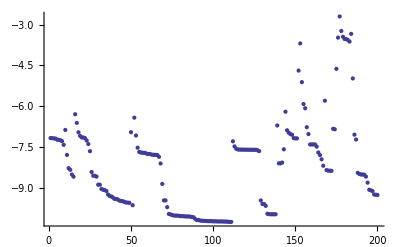

```mathematica
ListPlot[%]
```

```mathematica
Append[{},o]
```

{o}

## Canonization

```mathematica
mps=MPSProductState[10,BondDimension->15];
MPSNormalize[mps]
MPSCanonize[mps]
```

Part::pspec: Part specification i$ is neither an integer nor a list of integers.

General::stop: Further output of Part :: "pspec" will be suppressed during this calculation.

4.20148×10^10-1.78814×10^-6 ⅈ

1.

```mathematica
MPSNormalize[mps]
```

1.

```mathematica
{u,v,t}=SingularValueDecomposition[Flatten[mps[[10]],{{2},{1,3}}]];
(* Now convert the result to MPS form [spin, chi, 1] *)
mps[[10]]=Map[{Conjugate[#]}&,PadRight[t,{2,15}],{2}]  ;
(* Store the matrix to multiply the tensor on the left *)
xM=PadRight[u.v,{15,15}];
```

```mathematica
(* Now do the loop to the left until the first site *)
Do[
(* Start by multiplying the tensor with the matrix from the previous site *)
newTensor=mps[[s]].xM;
(* SVD of the new tensor, putting [chiL, spin*chiR] *)
{u,v,t}=SingularValueDecomposition[Flatten[newTensor,{{2},{1,3}}]];
(* Form the new tensor with the first row of t^dagger *)
mps[[s]]=(Partition[ConjugateTranspose[t],{15,15}][[1,All]]);
(* Prepare new right matrix *)
xM=PadRight[u.v,{15,15}];
,{s,10-1,2,-1}];
```

```mathematica
(* Finish off with the first tensor *)
newTensor=(#.xM&)/@mps[[1]];
(* SVD of the new tensor, putting [chiL=1, spin*chiR] *)
{u,v,t}=SingularValueDecomposition[Flatten[newTensor,{{2},{1,3}}]];
(* Form the new tensor with the first row of t^dagger *)
mps[[1]]=(Partition[ConjugateTranspose[t],{1,15}][[1,All]]);
(* And here we DROP the last normalization, hoping it is ok *)
```

```mathematica
Manipulate[Chop[(ConjugateTranspose[mps[[site,1]]].mps[[site,1]]+ConjugateTranspose[mps[[site,2]]].mps[[site,2]])]//MatrixForm,{site,1,10,1}]
```

Part::partd: Part specification mps ⟦ 10, 1 ⟧ is longer than depth of object.

Part::partd: Part specification mps ⟦ 10, 2 ⟧ is longer than depth of object.

General::stop: Further output of Part :: "partd" will be suppressed during this calculation.

Part::partw: Part 2 of ConjugateTranspose[t$1677] does not exist.

Part::partd: Part specification mps ⟦ 10, 1 ⟧ is longer than depth of object.

Part::partd: Part specification mps ⟦ 10, 2 ⟧ is longer than depth of object.

General::stop: Further output of Part :: "partd" will be suppressed during this calculation.

Part::partd: Part specification mps ⟦ 10, 1 ⟧ is longer than depth of object.

Part::partd: Part specification mps ⟦ 10, 2 ⟧ is longer than depth of object.

General::stop: Further output of Part :: "partd" will be suppressed during this calculation.

Part::partd: Part specification mps ⟦ 10, 1 ⟧ is longer than depth of object.

Part::partd: Part specification mps ⟦ 10, 2 ⟧ is longer than depth of object.

General::stop: Further output of Part :: "partd" will be suppressed during this calculation.

```mathematica
MPSCanonizationCheck[mps_]:=Module[{norm,numTensors,spin,id,χ},
numTensors=Length[mps];
spin=Length[mps[[1]]];
χ=Length[mps[[2,1]]];
id=IdentityMatrix[χ];
Sum[Chop[Total[Abs[Flatten[Sum[mps[[site,s]].ConjugateTranspose[mps[[site,s]]],{s,1,spin}]-id]]]],{site,2,numTensors-1}]+Chop[Total[Abs[Flatten[Sum[mps[[numTensors,s]].ConjugateTranspose[mps[[numTensors,s]]],{s,1,spin}]-id]]]-(χ-2)]
]
```

```mathematica
MPSCanonizationCheck[mps]
```

Right0

chung

True

```mathematica
Options[MPSCanonizationCheck]
```

{Sense→Right,Site→0}